```mathematica
SetDirectory[NotebookDirectory[]];
fns=FileNames["FORT_focus-2021-03-09.png"]
camdata=ImageData[Import[#],"Byte"]&/@fns;
(*camdata=Table[ImageData[ImageRotate[Image[camdata[[i]],"Byte"],π/180*13+π/2],"Byte"],{i,1,17}];*)
```

{FORT_focus-2021-03-09.png}

```mathematica
Gaussian[A_,x_,x_,wx_,wx_]:=A Exp[-x^2/wx^2-x^2/wx^2]
```

```mathematica
data3D=Flatten[MapIndexed[{#2[[1]],#2[[2]],#1}&,camdata[[1]],{2}],1];
```

```mathematica
Print[Show[
Image[camdata[[1]],"Byte"],ImageSize->1000
]];
```

-Graphics-

```mathematica
nlmf = NonlinearModelFit[data3D,{A0 Exp[-2(((x-x0)/ωx0)^2+((y-(960-y0))/ωy0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2+((y-(960-y1))/ωy1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2+((y-(960-y2))/ωy2)^2)]+A3 Exp[-2(((x-x3)/ωx3)^2+((y-(960-y3))/ωy3)^2)]+A4 Exp[-2(((x-x4)/ωx4)^2+((y-(960-y4))/ωy4)^2)]+b},{{x0,416},{y0,520},{ωx0,10},{ωy0,10},{A0,200},{x1,525},{y1,520},{ωx1,10},{ωy1,10},{A1,200},{x2,635},{y2,520},{ωx2,10},{ωy2,10},{A2,200},{x3,744},{y3,520},{ωx3,10},{ωy3,10},{A3,200},{x4,857},{y4,520},{ωx4,10},{ωy4,10},{A4,200},{b,0}},{y,x}]
%["ParameterTable"]
```

FittedModel[19.5515+220.193 ⅇ^(-2 (0.00083446 (-«17»+x)^2+0.000925312 («1»)^2))+107.882 ⅇ^(-2 («22» «1»+«1»))+161.619 ⅇ^(«1»)+150.517 ⅇ^(-2 («1»))+105.298 ⅇ^(-2 (0.000742308 (-857.509+x)^2+0.000842201 (-438.325+y)^2))]

General::munfl: Exp[-1411.27] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-901.756] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1032.85] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
x0 | 416.729 | 0.0324485 | 12842.8 | 0.
y0 | 518.052 | 0.0297897 | 17390.3 | 0.
ωx0 | 36.2337 | 0.0649628 | 557.76 | 0.
ωy0 | 33.2664 | 0.0596268 | 557.911 | 0.
A0 | 107.882 | 0.193225 | 558.324 | 0.
x1 | 525.902 | 0.0223271 | 23554.4 | 0.
y1 | 518.971 | 0.0192909 | 26902.4 | 0.
ωx1 | 38.782 | 0.0447073 | 867.466 | 0.
ωy1 | 33.5103 | 0.0386149 | 867.808 | 0.
A1 | 161.619 | 0.186094 | 868.477 | 0.
x2 | 635.96 | 0.0156354 | 40674.4 | 0.
y2 | 517.957 | 0.0148438 | 34893.8 | 0.
ωx2 | 34.6176 | 0.0313228 | 1105.19 | 0.
ωy2 | 32.8742 | 0.0297098 | 1106.51 | 0.
A2 | 220.193 | 0.198889 | 1107.12 | 0.
x3 | 744.472 | 0.025501 | 29193.9 | 0.
y3 | 519.439 | 0.0194782 | 26667.7 | 0.
ωx3 | 44.2719 | 0.0511369 | 865.752 | 0.
ωy3 | 33.8263 | 0.0389948 | 867.456 | 0.
A3 | 150.517 | 0.173412 | 867.971 | 0.
x4 | 857.509 | 0.03288 | 26080. | 0.
y4 | 521.675 | 0.0308633 | 16902.8 | 0.
ωx4 | 36.7035 | 0.0658537 | 557.349 | 0.
ωy4 | 34.4582 | 0.0617781 | 557.773 | 0.
A4 | 105.298 | 0.18865 | 558.165 | 0.
b | 19.5515 | 0.0038548 | 5071.99 | 0.

```mathematica
nlmf[y,x]
```

19.5515+220.193 ⅇ^(-2 (0.00083446 (-635.96+x)^2+0.000925312 (-442.043+y)^2))+107.882 ⅇ^(-2 (0.000761685 (-416.729+x)^2+0.000903624 (-441.948+y)^2))+161.619 ⅇ^(-2 (0.000664874 (-525.902+x)^2+0.00089052 (-441.029+y)^2))+150.517 ⅇ^(-2 (0.000510205 (-744.472+x)^2+0.000873961 (-440.561+y)^2))+105.298 ⅇ^(-2 (0.000742308 (-857.509+x)^2+0.000842201 (-438.325+y)^2))

General::munfl: Exp[-1036.29] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-713.954] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-904.561] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

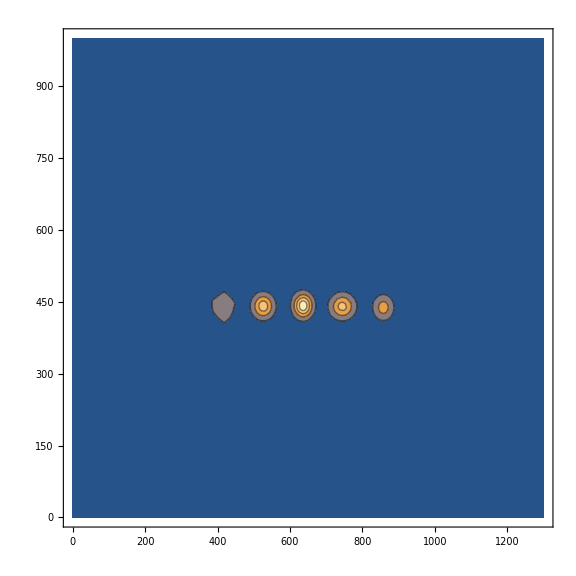

```mathematica
ContourPlot[nlmf[y,x],{x,0,1300},{y,0,1000},PlotRange->{0,350},ImageSize->Large]
```

General::munfl: Exp[-1102.03] is too small to represent as a normalized machine number; precision may be lost.

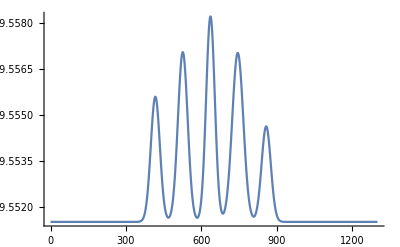

```mathematica
Plot[{nlmf[517,x]},{x,0,1300},PlotRange->All]
```

```mathematica
(*For[i=1,i <3, i++,{data3D=Flatten[MapIndexed[{#2[[1]],#2[[2]],#1}&,camdata[[i]],{2}],1];,sol1=NonlinearModelFit[data3D,{A0 Exp[-2(((x-x0)/ωx0)^2+((x+x0)/ωx0)^2)]+A1 Exp[-2(((x-x1)/ωx1)^2+((x+x1)/ωx1)^2)]+A2 Exp[-2(((x-x2)/ωx2)^2+((x+x2)/ωx2)^2)]+A3 Exp[-2(((x-x3)/ωx3)^2+((x+x3)/ωx3)^2)]+A4 Exp[-2(((x-x4)/ωx4)^2+((x+x4)/ωx4)^2)]+b},{{x0,92},{x0,73},{ωx0,4},{ωx0,4},{A0,200},{x1,102},{x1,73},{ωx1,4},{ωx1,4},{A1,200},{x2,111},{x2,73},{ωx2,4},{ωx2,4},{A2,200},{x3,120},{x3,73},{ωx3,4},{ωx3,4},{A3,200},{x4,130},{x4,73},{ωx4,4},{ωx4,4},{A4,200},{b,0}},{x,x}],fitvar1=sol1["BestFitParameters"],Print[fitvar1],Print[Show[{Image[camdata[[i]],"Bxte"],ListPlot[{{x0/.fitvar1,(x0/.fitvar1)}}],ListPlot[{{x1/.fitvar1,(x1/.fitvar1)}}],ListPlot[{{x2/.fitvar1,(x2/.fitvar1)}}],ListPlot[{{x3/.fitvar1,(x3/.fitvar1)}}],ListPlot[{{x4/.fitvar1,(x4/.fitvar1)}}]},ImageSize->1000]]}]*)
```

```mathematica
(*For[i=1,i <1000, i++,{data3D=Flatten[MapIndexed[{#2[[1]],#2[[2]],#1}&,camdata[[i]],{2}],1];,sol1=NonlinearModelFit[data3D,{A2 Exp[-2(((x-x2)/ωx2)^2+((x-(156 - x2))/ωx2)^2)]+b},{{x2,111},{x2,73},{ωx2,4},{ωx2,4},{A2,200},{b,0}},{x,x}],Print[sol1["ParameterTable"]],Print[sol1["ParameterErrors"]],fitvar1=sol1["BestFitParameters"],fiterr1=sol1["ParameterErrors"],Print[Show[{Image[camdata[[i]],"Bxte"],ListPlot[{{x2/.fitvar1,(x2/.fitvar1)}}]},ImageSize->1000]],Fortx  = Append[Fortx ,x2/.fitvar1],Fortx = Append[Fortx ,x2/.fitvar1],Fortxerr  = Append[Fortxerr ,fiterr1[[1]]],Fortxerr =  Append[Fortxerr ,fiterr1[[2]]]}]*)
```

```mathematica
Fortx = {};
Fortx = {};
Fortxerr = {};
Fortxerr = {};
```

```mathematica
For[i=1,i <3, i++,{data3D=Flatten[MapIndexed[{#2[[1]],#2[[2]],#1}&,camdata[[i]],{2}],1];,sol1=NonlinearModelFit[data3D,{A2 Exp[-2(((x-(1.4+x2))/ωx2)^2+((x-(156 - x2))/ωx2)^2)]+b},{{x2,111},{x2,74},{ωx2,5},{ωx2,4},{A2,200},{b,0}},{x,x}],Print[sol1["ParameterTable"]],fitvar1=sol1["BestFitParameters"],fiterr1=sol1["ParameterErrors"],Print[Show[{Image[camdata[[i]],"Bxte"],ListPlot[{{x2/.fitvar1,(x2/.fitvar1)}},PlotMarkers->{Automatic,Tinx}]},ImageSize->Full]],Fortx  = Append[Fortx ,x2/.fitvar1],Fortx = Append[Fortx ,x2/.fitvar1],Fortxerr  = Append[Fortxerr ,fiterr1[[1]]],Fortxerr =  Append[Fortxerr ,fiterr1[[2]]]}]
```

| Estimate | Standard Error | t-Statistic | P-Value
x2 | 109.934 | 0.018197 | 6041.32 | 9.947982681×10^-56753
x2 | 72.4264 | 0.0204422 | 3542.98 | 1.0740839510×10^-47948
ωx2 | 3.97499 | 0.0364074 | 109.181 | 1.220227636×10^-2254
ωx2 | 4.46544 | 0.0408995 | 109.181 | 1.220227622×10^-2254
A2 | 188.543 | 1.72625 | 109.221 | 4.3488034056×10^-2256
b | 18.7117 | 0.0233945 | 799.833 | 1.028538093×10^-23801

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
x2 | 110.034 | 0.0179908 | 6116.1 | 7.140898352×10^-56956
x2 | 72.4556 | 0.0201949 | 3587.81 | 6.653319625×10^-48156
ωx2 | 3.96341 | 0.0359948 | 110.111 | 2.784046846×10^-2288
ωx2 | 4.44897 | 0.0404046 | 110.111 | 2.784046897×10^-2288
A2 | 188.274 | 1.70924 | 110.151 | 9.716844936×10^-2290
b | 18.6987 | 0.0230873 | 809.913 | 3.1253420406×10^-23997

-Graphics-

```mathematica
Plotarrax = {};
Plotarrax2 = {};
Plotarrax3= {};
```

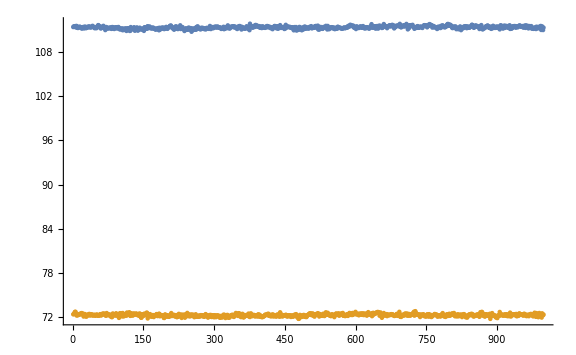

Histogram::hbins: The bin specification 0.05 cannot be used to determine either how many or which bins to use.

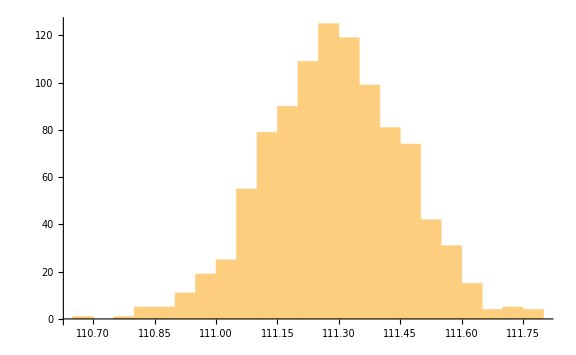

Histogram::hbins: The bin specification 0.05 cannot be used to determine either how many or which bins to use.

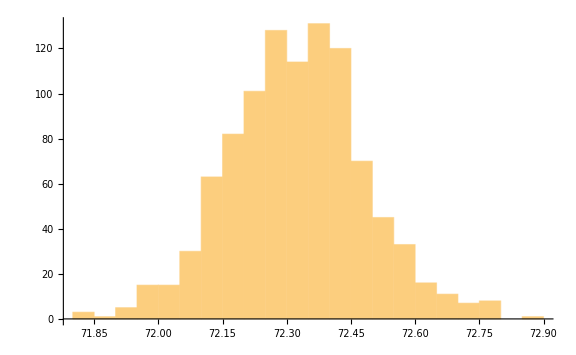

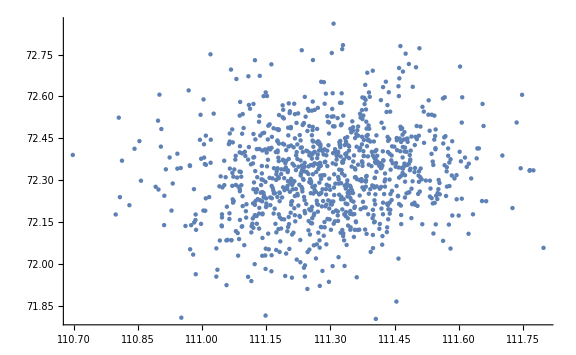

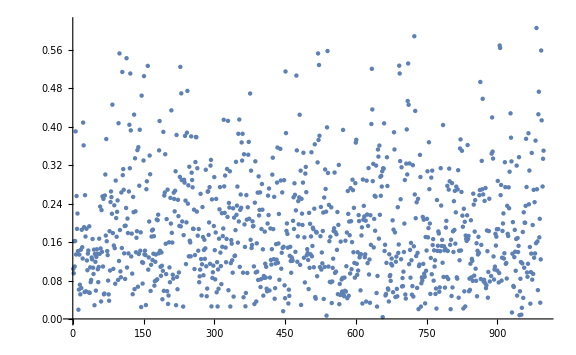

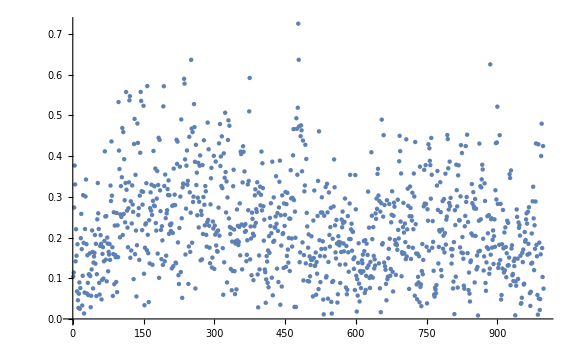

```mathematica
ListPlot[{Fortx,Fortx},ImageSize->Large]
Histogram[Fortxsave,0.05]
Histogram[Fortxsave,0.05]
For[i=1,i <1000, i++,Plotarrax =  Append[Plotarrax,{Fortx[[i]],Fortx[[i]]}]]
ListPlot[Plotarrax,ImageSize->Large]
For[i=2,i <1000, i++,{Dist =Sqrt[(Fortx[[i]]-Fortx[[i-1]])^2+(Fortx[[i]]-Fortx[[i-1]])^2],Plotarrax2 =  Append[Plotarrax2,Dist]}]
ListPlot[Plotarrax2,ImageSize->Large]
For[i=2,i <1000, i++,{Dist2 =Sqrt[(Fortx[[i]]-Fortx[[1]])^2+(Fortx[[i]]-Fortx[[1]])^2],Plotarrax3 =  Append[Plotarrax3,Dist2]}]
ListPlot[Plotarrax3,ImageSize->Large]
```

```mathematica
Fortxsave ={111.3338317864083,111.43390970179476,111.37711487388415,111.39919531135426,111.46376525334699,111.30341184904576,111.47348139510578,111.48974368471933,111.23621996655262,111.39695383354822,111.2040730772133,111.29262804702239,111.3110890600036,111.35352406575859,111.38938512281244,111.33447106533033,111.32660071878807,111.20288332265349,111.14410346670353,111.16254822007477,111.31113311329058,111.30322732662079,111.36763833562429,111.14740731397646,111.33648090263372,111.38747365432499,111.35745644794953,111.19204567291214,111.21077792526138,111.34008131874451,111.32979724188043,111.38292187328401,111.27481029231886,111.38906340730464,111.42493525770331,111.33331485189382,111.3487538662829,111.27213757774685,111.31821240552185,111.38791292342707,111.38489398292597,111.40707386646421,111.34398752449427,111.37514030113222,111.31942759389811,111.19489938662367,111.20068745404898,111.28309814338512,111.23363567622717,111.17476358399603,111.2819614394456,111.4186486088493,111.4052599604756,111.60726406686094,111.55516379515731,111.45798526689207,111.32065143305293,111.38440364998329,111.15404468703554,111.1974276259955,111.19225967923168,111.34898291764243,111.26340552445163,111.43984172191381,111.40695168223693,111.25900668619015,111.20779407402627,111.15408552996049,110.92446983108597,111.18154798804713,111.34609373578421,111.15203565266934,111.25854207959573,111.13441459676977,111.20095968876963,111.23049774015264,111.17945418469469,111.17688026167679,111.27405727023026,111.21962090119524,111.28466123929226,111.08525967405224,111.14797322785903,111.34672651053651,111.20564493421378,111.29071809364612,111.19599614526136,111.07204941357605,111.29299434216902,111.18192468416628,111.23749836117638,111.32263631210215,111.25702289128795,111.13713295563727,111.2687362519772,111.32796774074964,111.34784201523293,111.11544962830455,111.14918364764341,111.00370519577643,111.136295518403,111.11236735716975,111.0274424162638,111.12163984004052,111.12825549692116,110.90068155419348,111.12820726223063,110.9748048846045,111.07892385938797,110.94257219860071,111.08858099629046,111.17055286783521,111.0067982874116,110.8082409705714,111.13406989940826,111.10969257418294,111.11922511511517,111.18840564457081,111.06404962953133,111.16229188824136,110.80565952040087,110.83045611582712,111.33742891692313,111.08932867042431,111.17540128514522,111.12925458129236,111.04078679338609,111.09205726429153,111.09525541515275,111.3170943404035,110.9040528014135,110.84247697267035,111.17675742322612,110.99679457290097,111.13334193579992,111.29693653597153,111.18520934402999,110.85391840268152,110.90513313829513,111.16333793654546,111.07564647358282,111.25677456095653,111.18632729315762,111.04667313323,111.03358870315915,111.03612096029367,111.02071774305908,111.1201697380992,111.07111249214061,111.10403166035785,110.81315641016603,111.29306037794768,111.31689676886924,111.21605300914186,111.10781417344239,111.10018486200974,111.10856798360471,111.38243712359814,111.45447621712406,111.16487941432577,111.2639917238276,111.33814348982958,111.41945340467387,111.20185626195168,111.25781629581358,111.20348924437849,111.14410537699672,111.2523405799415,111.14390024262056,111.23942321616371,111.25472625468309,111.15617983340205,111.14078146360775,111.07184739512743,111.08214438978001,110.97153968079522,111.10138884451179,111.12043152149876,111.08858376091212,111.06436679564055,111.2009786131241,111.00477800292089,110.89739461712742,111.2464053992053,110.98483064186854,111.0522452565592,111.1499640470878,111.14010727572679,111.27445863659392,111.1653697492537,111.17851197544987,111.2784708028658,111.10786899872328,111.05746404331293,111.1277814606203,111.19224321223643,111.22990536554007,111.35612693581088,111.33606091021379,111.12816241089457,111.09180631423847,111.27196809564089,111.30140530438977,111.33221954449752,111.40311630773986,111.48942604042005,111.43284367289873,111.56392698995657,111.46022894348621,111.3133745227117,111.23349105601793,111.14051887342977,111.15800888818474,111.23490638733688,110.97211989531284,111.17001955735361,111.38128758531734,111.13564061726631,111.42785954752145,111.40415219715224,111.14094963672906,111.11539953008997,111.05964229439465,111.2108918594895,111.24084609272997,111.25285993779622,111.28840093408337,111.57704402943561,111.07082942244604,111.22134840386284,111.29672729031167,111.20861408253395,111.33156377990986,111.09518780687574,111.07275745611666,111.00510069940931,110.7984758712632,110.98552846091658,110.94045815223094,111.17638066377118,111.06288069161202,111.00896816047145,110.96898165128434,111.12332105799291,110.99814338334052,111.27591253063392,111.15623188833251,110.98181837803409,111.14155879123608,111.20040715428044,111.0779800415941,110.69815812168007,110.92888082415696,111.15419577515287,110.91210527238634,111.0520583977738,111.13407430951324,110.97951388800303,110.96151304295711,110.98131730111903,111.26011780881991,110.98527101365437,111.35513032044024,111.13358362716373,111.44013907052035,111.27795573027574,111.14145244914286,111.16296587139233,111.14966809058419,111.0940686400249,111.00775414056715,111.23127729812465,111.12036525662409,111.15947766761963,111.25287388922936,111.09304536166339,111.18956582522122,111.12382785680616,111.05710878021024,111.13033781563196,111.11446088257016,111.00913511459024,111.1413825381828,111.22303872839551,111.21131343708396,111.1872849162992,111.16236111141005,111.17631185267393,111.0867584160208,111.24370320356792,111.48737017745452,111.38147078344092,111.0652581463947,111.27471062435312,111.27517446189636,111.33976174701036,111.25444564081689,111.16796926635412,111.2711990929044,111.31926217258794,111.38380732836312,111.29747423606449,111.37635903741854,111.3943609366956,111.26629438283108,111.30076342721995,111.40329012753585,111.37843496083585,111.29062094082178,111.31070529423313,111.22989056380804,111.30126320236064,111.24054647995887,111.18313720720671,111.07936974254245,111.12388546279968,111.2384243228612,111.2013422211686,111.20828678005957,111.37829835316484,111.0459884063833,111.21171027837184,111.10334074680494,111.2754118220449,111.26842315232952,111.340904892953,111.17879342846477,111.38982377461282,111.57047239934964,111.24077974284755,111.19461572942471,111.25328821815658,111.12328431917597,111.35619992148413,111.33583578036419,111.27688937715283,111.40474079156962,111.37385170728182,111.40533242521708,111.41968155370493,111.43220846796389,111.42120383220175,111.26908109072086,111.35908877256225,111.39349266303951,111.32640429433922,111.17390199329459,111.30633439115378,111.07069668186915,111.23466640077596,111.38266364799242,111.4182095413596,111.2156349146713,111.48448366601856,111.43525154392233,111.25100223916908,111.18141080252099,111.00336116626225,111.370854879998,111.23540366325246,111.2138574333285,111.22151854126355,111.26646833682746,111.12455105420375,111.11598065548777,111.19299910826895,111.16681145199614,111.21710536880772,111.45271147692192,111.25444929839601,111.33121523075668,111.10270435617542,111.08825459398284,111.11881541858226,110.91162427016857,111.79829619511938,111.47817827000344,111.51528656925653,111.44417375679828,111.30905477961784,111.26145102985632,111.46077609525726,111.26829496458184,111.40562745368082,111.49220885914787,111.52314138935637,111.35716039533017,111.62917215882008,111.53275772426828,111.55254083752523,111.42315274669978,111.51488411740982,111.43859329770109,111.3615221731592,111.43283521486765,111.46692802016429,111.23991194032165,111.32991412866996,111.28643862927397,111.36403369044083,111.1967880993786,111.43885779667909,111.25107225521243,111.3847593941374,111.36004158134398,111.32787284083408,111.24080984322348,111.22306338712052,111.31847332696114,111.30654151861341,111.4105641160951,111.47315159596519,111.47455244777979,111.297119104809,111.39344073039242,111.3848010368986,111.3068871468774,111.34058726305654,111.35239458051326,111.18106175540684,111.24946078484852,111.20548121409145,111.23567222536751,111.04687063661125,111.27788907531253,111.34684619940997,111.27946216622403,111.47468304398373,111.47804081794094,111.42322315201031,111.3173183251141,111.17386302085734,111.2571712411938,111.45606510437014,111.1285130152535,111.12200718877142,111.27671325654407,111.35958164134016,111.42185465488042,111.60320341767691,111.35793424884625,111.21577156162925,111.30916593233991,111.26938542422583,111.32800081794944,111.23859387701636,111.2236317173024,111.36227817710898,111.07345457910046,111.14238976454862,111.14097303734354,111.64204310272986,111.25921376444923,111.30792314412093,111.42829608066785,111.414603197339,111.34081518326859,111.33859898293122,111.3492263192278,111.34663120497109,111.35754324067717,111.27095685368542,111.26140554590025,111.2180288605202,111.20011846404669,111.32064972489067,111.28676943396323,111.08356439986207,110.89189334007823,111.07909788026691,111.33783484111886,111.08779075239511,111.21227564740586,111.33960638012296,110.85740993283638,111.08451182779432,111.11791288143357,110.972404958298,110.95185697406794,111.14871416861217,111.36174554466429,111.21527148365327,111.2899494317711,111.04175640994598,111.03370675468169,110.89841926842348,111.08881564048652,111.26016592889953,110.99790337570221,111.27427019849517,111.37499620278737,111.32396377649604,111.39949194132221,111.09897260340536,111.32519206198097,111.20429074819402,111.24098084075639,111.14853136155824,111.27044060385639,111.15940217140873,111.13998351233249,111.29455964405832,111.3801143928259,111.23052454770665,111.3044394214794,111.46394937673374,111.17340824661274,111.18916518483409,111.27092364485796,111.31475869340959,111.22540090024235,111.23072136967124,111.3303876069005,111.46212891512002,111.46339829056338,111.48645888984268,111.34685518400436,111.20288147656407,111.22858226482323,111.52987440604178,110.99531142631474,111.36496644851232,110.98625393018807,111.14540646566616,111.18931264015685,111.35846367583427,111.14521327352952,111.18542204568978,111.1195806740165,111.0907964014004,111.15819190194614,111.34392206595523,111.34396923542864,111.23987186353136,111.30859199151716,111.25895678479759,111.40028921001801,111.37512471914123,111.3707652551063,111.00933065523931,111.49261096709125,111.28643894790156,111.20757841861172,111.04381616698402,111.19937588487248,111.17663905821593,111.28014145102111,111.20736036567769,111.32421999228656,111.32324277380239,111.24090640457582,111.15210546471867,111.27752055857565,111.15982753121921,111.2469519400982,111.04789830307945,111.13924653596679,111.17939673198362,111.24985342641315,111.0938948385141,111.1682703005247,111.37392482352479,111.36301576293341,111.18860407364706,111.25437346436176,111.23275299763637,111.22533412691733,111.25320922355516,111.18013919347996,111.17939961757983,111.0974099675361,111.13442972227759,111.14905490036462,111.2106029399773,111.234526718524,111.28190580521918,111.20888332444623,111.1674967809407,111.24869403553213,111.28697628041448,111.27900297053012,111.27399138472883,111.27065820794827,111.46479962108656,111.49745713199158,111.44957901205639,111.39023563537732,111.56322604712405,111.65577631408435,111.51119731829134,111.51848779942519,111.56619706406136,111.46895261342023,111.43664283059299,111.53934846384303,111.46783872752735,111.23705276776751,111.32610252423758,111.30989747740658,111.23327445817927,111.06484261616156,111.43785660314548,111.32327918149001,111.38402825859737,111.2767551291066,111.22102718641067,111.2075640906031,111.26918926329014,111.3553640540775,111.41973189970115,111.36946190831353,111.4076026910403,111.24008674713684,111.26336441771748,111.24233234694343,111.47256362977558,111.26704665861972,111.18985959671049,111.19202883612039,111.27162961693894,111.14121532858954,111.32490559219673,111.3074875220726,111.3257699556284,111.20834492308221,111.22475474443844,111.25942268642645,111.20224984171534,111.10972154942576,111.23345263476638,111.26226670653935,111.46886621784145,111.33024064909185,111.73542516020736,111.33580600112683,111.24034026769221,111.3272684283389,111.42323686684915,111.28672608332792,111.45516924132147,111.20140303206065,111.37401163119118,111.12044209407847,111.42977597987684,111.4697266388905,111.46132766694359,111.47598210483404,111.12389614585554,111.46073453964049,111.38334695882983,111.54007488574722,111.39924228601039,111.3863766478748,111.3210408261779,111.40228003151857,111.21021220490769,111.27663974086728,111.27400194054493,111.57229254228085,111.74813833671223,111.44091920010595,111.54737730894989,111.44574978120698,111.40772229580432,111.35732874554631,111.3649407530145,111.17958126291963,111.39625903307417,111.43459557530024,111.45954512753968,111.4606340021947,111.5940179910617,111.40716572490299,111.42410183000696,111.45543480552875,111.56905755588845,111.5718354697697,111.64718001068107,111.44342254883328,111.38790308549008,111.53413553120109,111.14074815196778,111.40366777246224,111.32404381585319,111.36861719002167,111.41584074174096,111.51898090321691,111.40183540772748,111.40238319939758,111.53955930197412,111.54067560807927,111.42574599089633,111.40828241075698,111.77459251882863,111.56353859686266,111.33661095610607,111.2907551886758,111.41613403733149,111.48372961976024,111.4269175433315,111.48272672071292,111.5784031748526,111.54574908806127,111.40069995185343,111.54320032741076,111.51063125553092,111.47310347885445,111.76558096283449,111.43140943581157,111.45836712376997,111.02020858311656,111.53685240787271,111.16740484151231,111.26032402411597,111.58103468731258,111.59524292735792,111.58394481144354,111.48075258105189,111.57807158196472,111.57525448036408,111.64362373678216,111.37937188684002,111.38158178557315,111.32957636228649,111.09485170903868,111.27690437367453,111.30758477319009,111.27868130864188,111.21726196736212,111.40954386737917,111.37842608128408,111.46977364854494,111.23091710607582,111.24699172091552,111.25520940372115,111.3163703147332,111.39975825878037,111.34978879711453,111.37529816153973,111.31790125724558,111.286037167403,111.21167192051965,111.41447013100944,111.47716599996924,111.54084391810465,111.59991321616276,111.55575567147689,111.57257833901261,111.54101273316724,111.46554339298446,111.47459385381377,111.29565852105294,111.60222821909959,111.40909635836794,111.62300017705216,111.49898843432406,111.74481893299651,111.63340258035826,111.65451724260053,111.61882151766787,111.58092372532086,111.54637247745188,111.26326642991406,111.39959511841738,111.49678028802522,111.41829644536915,111.28426203542772,111.35276697642718,111.36494607847375,111.31291739526092,111.2737469047102,111.25763996224542,111.07413801121753,111.15482401752256,111.2985240300065,111.40383734446831,111.22763522037626,111.23980879181632,111.30356156534279,111.19960456773595,111.49646324938941,111.28161523875906,111.4236870493436,111.54610196132361,111.56743899353033,111.35323086338768,111.44053474776587,111.34763000009683,111.2995951806371,111.33977306577852,111.3380936663686,111.39006440390348,111.56705657023872,111.58484406315198,111.72565755352078,111.766562700646,111.70203843122893,111.49794385680276,111.6071652595467,111.66423666790557,111.60525200176653,111.6236885192845,111.46488623475103,111.45360114053474,111.24747569427639,111.19145217560542,111.28832659497729,111.42270192699624,111.28957638427187,111.3220253321819,111.29339227991079,111.43873843868036,111.26036478679465,111.04686203174161,111.13342388405874,111.21709713444689,111.25846900437823,111.0582759476947,111.06414171859926,111.13817741974229,111.09341622349228,111.42776236266191,111.0554236487954,110.91566865401468,111.1726799354073,111.17355475459439,111.29517117638632,111.17856424860899,111.19716232328705,111.40778790072243,111.404572144252,111.37813712061212,111.38857965492994,111.45927513701679,111.34169634740295,111.18192713681636,111.28159056624985,111.43845909982562,111.31748969123139,111.30566918840145,111.24909123095867,111.27188181002339,111.31458318539444,111.38308297466823,111.46520186223957,111.54291184819259,111.65809324213735,111.61468760440835,111.53652707652788,111.46567543944988,111.22906154085463,111.31805566360619,111.32619598576456,111.54397673619648,111.40627777432067,111.53276404397554,111.44255318284817,111.48564998622034,111.37288511375515,111.33702964777765,111.40837922654528,111.30630830602145,111.06900011522154,111.25804630732867,111.48360428419838,111.45924727935963,111.60825314918041,111.32774681430632,111.06790119482652,111.01692728071262,111.14135814928957,111.2173019202841,111.18944728287983,111.18404399401868,111.25736025714453,111.40603812987676,111.40176406494802,111.47140403586577,111.41564219440777,111.5532022640769,111.51015326330527,111.41870312003341,111.2625446116927,111.22287083409067,111.238406515674,111.40636686392554,111.17659511591661,111.08889876385274,111.33259404719969,111.3749887291246,111.17954029478706,111.5134998959318,111.38343968579295,111.35411352930815,111.25554366727495,111.21427445142703,111.24892269404657,111.33329888759657,111.41575696174311,111.30535464809134,111.24640321393291,111.40380129217846,111.29748520117539,111.3728530744272,111.29018153825116,111.0199605161241,111.33360040036042,111.59012939677696,111.36063035640872,111.37825655362793,111.49803401254026,111.3195251714088,111.12611789402775,111.34579683834805,111.42169641016935,111.54569952270202,111.22006443340409,111.44330746913204,111.48592870012747,111.43517017884561,111.48681637511997,111.34694700620108,111.24481452147619,111.3465601196856,111.46540322897711,111.29718545517963,111.58403640325382,111.08054088676059,111.40283605119947,111.12017269469407,111.16341252297681,111.15389381803199,111.25412038023256,111.4442548749565,111.40457382053063,111.46903762891493,111.36889634886629,111.48024029851114,111.34248067776022,111.24394104716401,111.39094133335739,111.39875259944642,111.43560022391944,111.2916151147911,111.40766399433079,111.43440551363953,111.52927154010836,111.537025961447,111.5321220495454,111.48778553497361,111.36972553820844,111.3679860897617,111.3857342634478,111.48010722640208,111.31186728912112,111.34123310147794,111.25701358031623,111.35133736170303,111.54483786688954,111.45482405443606,111.21960748633535,111.57543927000934,111.40110512390945,111.47439245335427,111.39798594728418,111.49124348512622,111.15126637808461,111.22784891406606,111.47766239924937,111.32808538247528,111.33499518721433,111.35322666560798,111.46947402996815,111.12486084261512,111.19699679867233,111.12518674333845,111.17173900054802,111.0881485253072,111.21428905907369,111.28495137318703,111.2049829641833,111.2027267234596,111.06851964966371,111.39221063004548,111.17998334481354,111.32814131478678,111.32345122357987,111.16281739628032,111.37388300906689,111.3055263776157,111.34362843352032,111.37729394842034,111.48967936669183,110.94252872127937,111.14866799777447,111.43346424336757,111.25851296942777,110.93176151147803,111.26342424063365} ;
Fortysave = {72.42639031732209,72.45555456437496,72.53179699440709,72.69219881720224,72.78021431908165,72.75539194516452,72.40379202470957,72.27059033443525,72.30559910880329,72.40223523093638,72.29561572292111,72.40641526685825,72.41165216867901,72.36768655788553,72.49665748149347,72.4512258765732,72.40179880740893,72.57540845647952,72.60125291174774,72.41653440318248,72.40239174521285,72.52791003408703,72.12414983014943,72.41075990141111,72.43952958927544,72.46273732924959,72.2068019599553,72.16105915294019,72.10674799037214,72.24288849575586,72.36420466497406,72.2778295254786,72.36027890245694,72.4453818842674,72.48737828891939,72.3176922256281,72.26579818112383,72.3410693555638,72.40225116117567,72.44391299317674,72.31598513947903,72.29405674812448,72.2620345800315,72.36396207308597,72.2887434695879,72.36159005199633,72.33373793061106,72.22662495208694,72.33475368768879,72.3326994058698,72.40491334106368,72.3563767434255,72.25186740371664,72.23480991935773,72.29094474177074,72.24356930711082,72.33879810049213,72.45831406966238,72.41267243490887,72.27224847138902,72.3082188560757,72.4718554852069,72.3614603018987,72.54585902879747,72.45982899869476,72.49140051159036,72.49091855912303,72.49561911788385,72.38204923073285,72.22596428079046,72.2813119451634,72.60177868998908,72.47993999680234,72.41231894382882,72.29730473978387,72.37143029014138,72.36923886127593,72.40691911873938,72.25217779463374,72.33700359120726,72.10239676754836,72.27764652545655,72.03186001269637,72.1238487228,72.54714917359921,72.38999856221699,72.34651919819463,72.43598724902428,72.35140262887923,72.25459120351427,72.302245465225,72.57748676458016,72.37803415299965,72.25599553192681,72.43611337291956,72.19640966780597,72.27516309417628,71.94038163083381,72.05623306228462,72.58964993997373,72.46040928432902,72.55637322442813,72.53879760128784,72.29290177905565,72.14542537139843,72.6065799197613,72.41192283989672,72.14021148466661,72.38821097220374,72.39560449236568,72.26855894867482,72.2542222935199,72.35852732792917,72.24031191034422,72.67385625692059,72.56985432009364,72.36107387391336,72.52600170929516,72.4679190976909,72.71491931140888,72.52435463792257,72.21151822700678,72.27620052204581,72.5805854048636,72.48310287197975,72.31159263579943,72.27898257020036,72.28309065723585,72.5371510184741,72.52277573630863,72.42085192365776,72.41324118673727,72.40107304592726,72.53457141577823,72.4097704529133,72.4674033934081,72.32295904761021,72.44054405778271,72.48378887059243,72.23634163293195,72.33932581002925,72.54938181363768,72.16175198674476,72.13607237270321,71.9563168990766,71.98089192324974,72.4456719712274,72.38190601147102,72.32708271546467,72.21491091791964,72.37057902261432,72.52959068796837,72.3973221853016,72.29714403833303,72.37440838558989,72.40230296048348,72.67229381453964,72.58800298407725,71.86718669725694,72.30744340941173,72.28086555995297,72.3853206733244,72.19948479605456,72.46106988768669,72.16405449616436,72.14397820398227,72.23982095865308,72.10680481540349,72.25560493949419,72.33266907695169,72.14734121519305,72.05391596882978,72.22549945622931,72.23239297603347,72.31029406036151,72.3540217998628,72.38772344626155,72.46600965276123,72.26140881756912,72.18264263446913,72.33625643730932,72.42917592398821,72.51357949040855,72.47686891454701,72.15843066870069,72.28327139972585,72.23582726109389,72.32510004494037,72.2920359225357,72.27309831443233,72.31185592401751,72.30576530624391,71.95556840633393,71.9258710555458,72.17296612368591,72.42820287814723,72.08729487689018,72.1798946217833,72.27101667286156,72.2685701939995,72.31346716241647,72.11348365659408,72.12377725752567,72.08609149610731,72.22904343647635,72.16543674340736,72.21679940174406,72.43214402664883,72.60154081279381,72.19275670145568,72.35324016100084,72.21760803923512,72.3093290282232,72.34292156375479,72.35174986039878,72.19928112615565,72.12474448192866,72.22912779442427,72.3249361187301,72.3090572369526,72.03072794573306,72.11434365173103,72.08771064533428,72.28426792772993,72.49454807051161,72.39789540189241,72.20752344151059,72.1422026836989,72.28082172099546,72.40127603390988,71.93764607704422,72.2131625674749,72.37473302948052,72.20830173471806,72.22082164274991,72.38164049426571,72.17839075197536,71.96489757959183,72.34446979029056,72.44281475139553,72.42976193820064,72.2360333084842,72.6217969859867,72.17270978280946,72.37749762766789,72.36282486730059,72.4144998722093,72.14986674669629,72.18181604564295,72.32985176557138,72.3744865434385,72.39114067377174,72.19235306210874,72.37380382384896,72.24531899061112,72.3704816761722,72.20195474795769,72.03403189531733,72.13735987805684,72.26888423751153,72.43916003001931,72.1783377968641,72.09816320270409,72.12799665178401,72.19407904824052,72.1338773352009,72.09453401724971,72.28048884587655,72.20517646499859,72.13617760309765,72.19177904282031,72.32548670534133,72.26865556533303,72.23944010030496,72.30442692010759,72.13491096266094,72.275552226268,72.21279979413863,72.08560924432403,72.2332715352145,72.35748161722408,72.46005405680205,72.17898937053951,72.25203803027959,72.29778240028884,72.23927073094967,71.97546552838016,72.24094764344002,72.09060058071104,72.21602652382094,72.3422168833865,72.2980498385743,72.34245178158893,72.08584014869087,72.0598022314562,72.30018469826749,72.29829021790141,72.25392386307905,72.21322371174905,72.02583923634919,72.31406554040205,72.19984573147318,72.2236857678192,72.04454143117026,72.25913949499893,72.21572049296863,72.27464197490364,72.26729663756488,72.21334745739914,72.15388873005473,72.00772587136927,72.22448111516223,71.95674241415928,72.08225793657304,72.11886624974724,72.1760531915341,71.98806952403806,72.13371043948673,72.30612235211947,72.38706949022375,72.13887831421735,72.35964312437203,72.16722899577006,71.92318047819764,72.0716190944,72.16487080822115,72.12621371301684,72.35635783882586,72.24457542086998,71.99666733249883,71.95869779371152,72.19297838524986,72.00091373712758,72.20166085327267,72.21759331112565,72.31765164321172,72.21477457040658,72.3684030226304,72.240408753974,72.34558109332913,72.11555983142264,72.07045293109587,72.216563085946,72.31174824087469,72.43902203264189,72.61137954341625,72.32198805877337,72.49357513321097,72.48241584036558,72.26083595164945,72.20306301264583,72.58700651821782,72.57424792892385,72.25780003751609,72.16122969407389,72.29410114623934,72.04455308756576,72.19239207005883,72.19737840690275,72.49812795454696,72.11321086277123,72.01718243180383,72.02127920140838,72.33342353579864,72.13680291537393,72.26538704238152,72.26406263203648,72.24438524202182,72.34903377245276,72.29037681100047,72.23314511524451,72.19006674806694,72.53166266321571,72.16428190714473,72.14034938023124,72.05912565981532,72.40245976783231,72.5630202856899,72.26255291600721,72.32206254068471,72.17556453903231,72.21573029275267,72.22748796968017,72.36381637520586,72.29700281540565,72.29974049171817,72.1235819444636,72.30719551927264,72.29924033403165,72.26882219556552,72.17915938379114,72.1436296552112,72.39528170744659,72.42046805759915,72.13227286841546,72.34516417434243,72.34896732883519,72.10134557662405,72.1514723468879,72.1229384005166,72.03870925592885,72.18142567401085,72.05307636781724,72.10913339954045,72.1408615480595,72.23428036746685,72.19698576305673,72.37664246163231,72.31240705569778,72.39771932323792,72.36679288141258,72.36015531227146,72.41760277798078,72.4070110176625,72.2690531591851,72.48518333991399,72.22490897190015,72.2648488602811,72.17876594118702,72.25700174532874,72.15499187084514,72.25937680938573,72.40142248054707,72.16766628880758,72.41122745356753,72.23738982590244,72.13280740051482,72.29572091535174,72.25377934256763,72.22059621300234,72.1740972573063,72.11449066255692,72.2056193285688,72.40830808228192,72.2667524044592,72.38355459049038,72.35596990584004,72.15371048094913,72.10109460922493,72.70695711942349,72.45140271069978,72.20075449566407,72.24786185889522,72.37971435383831,72.12286741892723,72.24091097160087,72.24673296743083,72.3045436622462,72.31358583797889,72.30163741028487,72.25840839011967,72.37883235629409,72.32227242300354,72.14556100447905,72.30380655190736,72.12734046422821,72.25604770752389,72.28808407175455,72.22809424235867,72.180167790839,72.3110648473034,72.18839336595111,72.06816344071413,72.15383373540567,72.28075910183122,72.2489993769679,72.13260339804364,72.11183723599075,72.27739387143562,72.28386225598412,72.39718482300422,72.33185790109373,72.26838615370059,72.45518606988004,72.29893554145279,72.03122652128393,72.14552406958586,72.05404449581071,71.80956424069054,71.81719162924215,71.95396124039696,72.35312648656499,72.2689623656145,72.08535182310253,72.05737862594208,72.26765468059214,72.15893582364649,72.25338887535459,72.14477996205132,72.35304444926716,72.2751247164669,72.11310997348566,72.10513367719497,72.06872981710345,72.29014859659708,72.05544765527084,72.18288788245214,72.2949413445903,72.35819266883146,72.41079336443485,72.35173914655104,72.40954915907113,72.57287279147693,72.4430827836912,72.55558518053772,72.49182340621772,72.30190700055317,72.43135241138373,72.55941637653852,72.37452601411744,72.21030025313017,72.31775364339376,72.11087817360271,72.44982878609993,72.4042563009288,72.36893794848912,72.48444819381697,72.37687862778002,72.46203810530652,72.58636255347288,72.44527239098213,72.49272513080444,72.12361696061765,72.47029940846743,72.37181961096834,72.33938171901806,72.24524297497568,72.33980432253692,72.21816415972765,72.33029163290945,72.40055338362131,72.37981457204717,72.42136026198332,72.19096596409966,72.27460603977191,72.58188840644467,72.70442489046403,72.5194209828671,72.52470690830565,72.35594190983393,72.6346238046311,72.41128309446822,72.48657793702523,72.31460943523065,72.26979905282273,72.34340561660645,72.20727373194041,72.18471882732455,72.38558406253828,72.41864305263472,72.38965115611347,72.34046233121865,72.35201341482554,72.21175465497177,72.04427200814307,72.27514012225324,72.30404941561493,72.48013949235104,72.54897578967359,72.46688422140113,72.3438341169124,72.42903194201106,72.47941082433466,72.5684342229149,72.25461803656201,72.27641826182294,72.34890487180662,72.39030570149767,72.53373049342967,72.48236704538517,72.48732728928736,72.53058188674045,72.61465867611498,72.22593877974712,72.26984037495373,72.26860942514205,72.22317613405821,72.18177095844244,72.32300635158471,72.36515320484585,72.25571707239583,72.43559015990856,72.3926355349605,72.21026409584426,72.42652385236778,72.42055822478797,72.61442355119813,72.59305367874305,72.57340239187079,72.34259524685342,72.54598011680123,72.45405553974491,72.32708533740625,72.61516635697214,72.36744707358208,72.4865156528165,72.40231094279091,72.57757039563128,72.49316469872856,72.76526932266906,72.43896619265252,72.4475676791417,72.44107611415293,72.40992440316117,72.4216581478565,72.40562890206038,72.28988565712358,72.48416130543359,72.389265380499,72.40643389852462,72.53824577831439,72.40890998911838,72.36282903697997,72.55210436064021,72.5278922430815,72.3510924088178,72.3301525449887,72.55258690316411,72.33917368748111,72.43998427766908,72.4070105903102,72.49723621561694,72.52898100935288,72.24163092662411,72.424670866937,72.53968066369428,72.73021418227279,72.42132572711346,72.41939823471425,72.41805153156633,72.4008004827494,72.46355362418248,72.53127300595587,72.40705960788409,72.172982774685,72.59862549241998,72.32523349820343,72.63357070564493,72.5740653766153,72.45158779857262,72.48858038036528,72.55127079305291,72.57340132035587,72.65286794078002,72.68910581694284,72.66483552260796,72.75310023956598,72.72969871992994,72.701810446808,72.55361410779017,72.23342757048124,72.38923824768801,72.68488248865958,72.43692420856934,72.14032209675311,71.95255126521477,72.25276463041439,72.24004035212367,72.34713620817844,72.6060248277545,72.33851484078477,72.24531066204389,72.36152404084338,72.33081910986422,72.34353794202909,72.45999676722845,72.17892668199208,72.35116577993655,72.40174729769025,72.34621238390719,72.30990629978125,72.31892085112243,72.33272517674969,72.37075861510152,72.4434986754874,72.45812243634805,72.33244067944063,72.41445578705229,72.38918074566872,72.38597895280837,72.27118740652937,72.20709091085584,72.20900611868743,72.23288676488163,72.2462981359266,72.3556416271988,72.43442461712281,72.49457240514414,72.44752526686896,72.21784366999327,72.35533440945239,72.25138918122657,72.77230296005852,72.33603937012172,72.08411322997684,72.1871893658353,72.07165268122533,72.36155136938612,72.35992200240497,72.29666076680923,72.25700944227027,72.27996873626131,72.41537617568628,72.27978605249751,72.5315572125784,72.49246122593811,72.47273529432215,72.33478913594543,72.5447533620018,72.24405788303493,72.36327180371113,72.23669691564602,72.48648205665148,72.42038344417573,72.37576338843601,72.2326665147523,72.3177655240724,72.43786533640143,72.36399089929745,72.41441211289397,72.41441845234951,72.59516149328311,72.64161482759998,72.78361541773718,72.24376201403794,72.42820909818955,72.86031031840012,72.65257196685477,72.5368793571029,72.38829937554434,72.44487966391403,72.34204831209954,72.41629443254689,72.40370305947921,72.2940373487213,72.38942329421111,72.05817103939222,72.34947621721274,72.35221332728808,72.39941683205969,72.31885892210603,72.28879847167812,72.35203389286174,72.44801051834574,72.2549652489862,72.17454879782719,72.2403683423675,72.27802740162418,72.1103537807437,72.17647411539383,72.31867423014337,72.42562279647572,72.40241245141594,72.26036242190253,72.10937392754211,72.45571920940523,72.34351347151686,72.17897260905221,72.22661103281081,72.34841900791308,72.0566039212076,72.14303117203758,72.26639753924552,72.19516953940621,72.32996709046097,72.34362352212455,72.39295406117641,72.47782624475538,72.3563524943024,72.35739778986033,72.4071128801877,72.3927354064202,72.22654144202882,72.11001562877986,72.1607930723147,72.30945406923055,72.28477333732548,72.22953900410435,72.21381570939172,72.11841442886495,72.22052632002018,72.31835758710072,72.37213204567885,72.48223063734217,72.59723306089155,72.25494195122799,72.25166108400938,72.13218198168123,72.26665491446913,72.21530190706649,72.06954340354625,72.25253593424766,72.35453140490957,72.44012746821299,72.20139077946088,72.33686479782263,72.38913272327203,72.2134518433577,72.40679614149297,72.22588720518674,72.36844604579706,72.35995449871568,72.31566334307006,72.36208325653129,72.55554517274955,72.5215698796835,72.36700744938395,72.40414520366846,72.6099901393481,72.42740390683139,72.16236202685131,72.22102706699175,72.35308278857201,72.17895267157566,72.18169091732827,72.17585680126481,72.44241047078407,72.20610452990852,72.1623222724007,72.28340143367831,72.39715293047414,72.27794219703028,72.31163772560582,72.33976135600129,72.40170376592052,72.05153110770917,72.22888782466804,72.3813277115613,72.37014789273839,72.46101038040598,72.40362199918113,72.20304786190921,72.17928737384112,72.02068819181419,72.13888686667634,72.16813403279145,71.97677852336695,72.3030997230056,72.18894208831816,72.361348062291,72.34025521189328,72.43095859511844,72.38812457198414,72.29579875338216,72.48417091224114,72.44599644006349,72.49463907013592,72.38169133948362,72.39409178522526,72.14407194116681,72.16976399126571,72.15541186373886,72.33710903235215,72.21981777372964,72.31742097159778,72.242571610946,72.37177806559744,72.39094133447692,72.30483345121935,72.43414079229034,72.27873095373485,72.18671589206221,72.08662703419985,72.27720691207244,72.7160981547951,72.6366140383108,72.59711821575954,72.769267297277,72.69620860105665,72.24068271397391,72.46818614540575,72.44040725604058,72.37402409723697,72.12833198794097,72.1468204389459,72.37528648118908,72.43922146948127,72.44602986452303,72.27044266390544,72.30175764245519,72.31164744024011,72.27684027437327,72.18163093800581,72.42876861999495,72.40518589673214,71.80517828985187,72.43952609169989,72.42223233643377,72.17915552710187,72.59663514019833,72.30820445579651,72.30394725274822,72.30077396174421,72.22416540428822,72.19464925673243,72.29549980966071,72.12173562245577,71.99444577772312,72.14454448430531,71.9937918807986,71.91220097446042,72.15261719547699,72.3065472362221,72.29748542600147,72.24954001063223,72.7407829544911,72.28170712011497,72.30716703134264,72.46575394040256,72.38800405723431,72.34440204276973,72.3034403363836,72.25755445127596,72.25334318304179,72.35361229774155,72.41125376162195,72.38969235176896,72.23004332719321,72.33653751055675,72.4414228899886,72.37404060182423,72.18549029044627,72.33020734661513,72.19071405812587,72.43766970127562,72.28021281766017,72.17473998809496,72.66257349240093,72.38074839731654,72.13063426978867,72.4558356045799,72.44651628659405,72.354940618785,72.42192143856249,72.36588728405329,72.3823714767363,72.30155260897533,72.44980797404351,72.42490881648152,72.40640690905279,72.48460346466963,72.16539317633172,72.19707334933891,72.28457054051845,72.36159333789975,72.21178731240563,72.53404305559929,72.53490591923901,72.47755163885317,72.4065949339877,72.41625659661818,72.40759410499633,72.42242160070965,72.35556811807753,72.2885793414042,72.25608885132375,72.4614077784936,72.51118618061855,72.45884785604444,72.28005410622788,72.2695578270794,72.38824454922396,72.17589540853216,72.23903895226307,72.28214480065485,72.21513322667818,72.39932363658397,72.1732318797365,72.35512474877348,72.36338308688885,72.39439885655733,72.49022862690963,72.41955174312925,72.44672425224306,72.40826651726967,72.22641137535467,72.14495373855412,72.4004174717518,72.41857255511086,72.65120416126359,72.5407680129329,72.16943028189996,72.08664078072215,72.59880655197561,72.43173840067861,72.36775638568368,72.42751411664703,72.03280131030091,72.45624661822717,72.61169863075874,72.40676263099762,72.40448462718224,72.45684008072094,72.34232957789288,71.9838221165384,72.56917078768265,72.35603138883384,72.2891405106696,72.402147800956};
Fortxerrsave = {0.01819699792604944,0.017990849241631496,0.018321029338821567,0.018561674715268723,0.017988929997456993,0.01980363790631317,0.01929486528098848,0.01783572123132225,0.019461625631978823,0.018335655408269303,0.018917366281166182,0.018389897939406936,0.019896982757056973,0.01912540616607746,0.018949232310214264,0.01786078528768568,0.018343716521413655,0.018917492844286354,0.018460793442364894,0.018341221779328242,0.018763332638270437,0.018518186778426236,0.017843939904896248,0.019344131291987563,0.018659032181067677,0.01936015755643669,0.018534816408498447,0.01890400047011163,0.018954887471171637,0.01929880264313473,0.018400122931801363,0.018491292112781603,0.018837670187068185,0.01845637936976533,0.018276210923444895,0.018796866070146648,0.018489467815210645,0.019182583259062205,0.01824763077986807,0.018610454328263228,0.01812437402280924,0.01861686366308895,0.018444482305117787,0.018440387165563923,0.018808171851252335,0.019215188514633958,0.01822613402344678,0.01869493306224316,0.0187824677386592,0.01818536449481207,0.019284607560893258,0.018641186272830273,0.01870544081881401,0.018202732064340203,0.01909863405810862,0.018831854080258128,0.019566918816014602,0.019740923061769125,0.019174269721010828,0.01899187853486936,0.01992142918162155,0.018642989049523818,0.0190495905707862,0.019605425909098483,0.018831339444239627,0.018676612533691753,0.020014208341237495,0.019716569545114526,0.01857752478719734,0.020758557128202976,0.019383413480739204,0.020120925460383975,0.01908794042117283,0.018213021252270402,0.018653405648123317,0.018300419277080118,0.01805256983464543,0.018577938118440443,0.01845160824410111,0.01840111634572112,0.017760363661627202,0.01817229638320068,0.01855741136296545,0.017405306664065258,0.018093516937056825,0.018358797072518335,0.018217411472333873,0.019156269789743424,0.01832932129814228,0.01922517693460685,0.018518201405613775,0.0175164561370333,0.019068870964624396,0.018529202022542667,0.018879939717563885,0.018077168266905436,0.018111422103090132,0.019140083171356934,0.01949952547355539,0.019168061479476705,0.018567046276959,0.017830866679080515,0.01840115520861033,0.018365152604932326,0.01837656113618747,0.01787530254581341,0.01823334488407981,0.01804870732130322,0.01870715453775343,0.019740702122894055,0.018298155566007338,0.018622910461275407,0.018900479338042724,0.018541447776460704,0.01820938904647967,0.018810782801230788,0.018360692022069493,0.017460351213799345,0.018453204424709563,0.01778662346018858,0.019540519768312628,0.019008429928448898,0.018298883180168594,0.018855683733884267,0.018643706377041068,0.018254093744409374,0.017748396179152116,0.018992296609863204,0.01842790377879981,0.018149988997691945,0.01936830166794219,0.01875858776938641,0.019222038077940688,0.019301732403660874,0.019155412197319716,0.019106589242800672,0.0191814714700296,0.019318421422408447,0.01949038490875104,0.01879866636689004,0.01887437907825852,0.01878688654202984,0.019246369296202683,0.019028258718526734,0.018340614898285475,0.019389240582633872,0.019449096131046215,0.01851415127971887,0.019030941581710238,0.01945100184515263,0.020463201370805317,0.018747142836183884,0.018158632319001278,0.01891861987459227,0.01943960240348027,0.018535792479417383,0.020136459403205893,0.02023571546348707,0.018740076493125992,0.019197744838591213,0.01871533447556385,0.018840076424779015,0.01883695169617233,0.01912093988207309,0.018749906472513157,0.018678600233605416,0.01969965951042632,0.019166111643880598,0.01880452772612439,0.019499640727218917,0.01839459880234178,0.018895615813347477,0.019126527375426618,0.018484041306730857,0.018938264221111892,0.020091161088243388,0.019196463025868245,0.019770116929782453,0.01982137284972944,0.01910172924176825,0.018912306288006886,0.018452813811040815,0.019753559137639702,0.018103240408014618,0.018053663854460396,0.018946315841104053,0.019338914094106023,0.017419607179079064,0.01951104490097999,0.01876440947060128,0.019495360072224024,0.018680639448778378,0.018081822753185314,0.017981599095834615,0.018220670811631343,0.019251151292854707,0.018917636919463323,0.019786137222746764,0.01874661615432843,0.01938964616340701,0.01923618124682709,0.0186865673943645,0.017998833486733697,0.01897384368881235,0.018806824976247465,0.018927054629549675,0.018583109539570007,0.018892487288268395,0.018470742082469224,0.01808617851479317,0.019522896116570772,0.01824082465520532,0.01828249240417716,0.018171372744036194,0.019893686738688722,0.01960165621384089,0.018429464540402705,0.01835374039621652,0.019071413716540453,0.01848990634791747,0.018583846194647865,0.01838840527105521,0.01801177610496518,0.018438427438873948,0.019896598402062584,0.019769639822717892,0.0193875523753137,0.01854981779857162,0.01901110644402408,0.01909214453012416,0.017693430667488623,0.019053311066522225,0.018888820821909406,0.01840317623244085,0.01784942769875329,0.01908487933437675,0.018673946007549493,0.019332152932461044,0.018572694558344805,0.018496921305181737,0.018698610192916146,0.017770927374330378,0.018821400274679756,0.018529406217614306,0.017743285943111448,0.017638724849690028,0.018420276899364825,0.018881620176141565,0.01944316662952359,0.018211563581798863,0.018777255842442192,0.019616241035109457,0.01780640853616841,0.01775580983329534,0.018477631158231193,0.018005173927095882,0.01792835912225135,0.01890291546260911,0.017447156360693994,0.018435630730494684,0.018376813865887662,0.01853616321842415,0.01871889374408548,0.01777758918942553,0.017984814086663675,0.019120254179266653,0.018080973959490623,0.018325149205634012,0.018344573132206367,0.018362057931532765,0.01794897098180352,0.01843558540356334,0.01797619027591795,0.017972267515435375,0.017820835998643644,0.017851993852568877,0.01785940170875824,0.018319952125541033,0.018111732494792095,0.017765665605426976,0.01874607634073626,0.017770775562426424,0.01839059661951549,0.018372132521058723,0.01832172217378302,0.018238579953776406,0.01861875277003288,0.01874213699008204,0.01879672628402221,0.018117456349303583,0.01792905671336012,0.018640223343751084,0.017521083326975603,0.017734759783787704,0.019126360613423668,0.017094796443000687,0.018042327431666946,0.01895918345371772,0.01791905969732239,0.017603354028542996,0.018591186433368535,0.019113547404072233,0.018536054700954114,0.018382797694004954,0.0180637660633408,0.018760722621664633,0.017658063676775686,0.018053064052433995,0.01773554314096787,0.01799040854305178,0.018110599422441327,0.017592463466091734,0.018106697044840923,0.018131313607874636,0.01805266967966814,0.01837070862820107,0.017718052008402402,0.01802242212225135,0.01813958286691251,0.017535852612403716,0.01838864101027481,0.01841681187662121,0.018373591847348453,0.017745609775219127,0.01818948693521765,0.017510239381122217,0.01809726517890765,0.0176883666873167,0.017699277876697665,0.018051442146576863,0.017903343485814568,0.018571304071081467,0.018480667870173228,0.01877630206423122,0.01856840819260072,0.01743926804358569,0.01787890862736949,0.018291340866942103,0.017913999077059803,0.018942518938652862,0.01745927657988298,0.017973908442744702,0.01805371022406285,0.017484280276028802,0.01780096394293369,0.017572303234577293,0.01966139676327004,0.019060809076697036,0.01855834735975188,0.018984402791319514,0.017413839702312223,0.0184300112409098,0.01886790393478895,0.017829738360540873,0.019601015122951232,0.018609487615338014,0.017846772806545397,0.018870194096398784,0.01897077473573665,0.019043679456316204,0.019459166551189674,0.01820319189883542,0.01921869569791989,0.018213361759991567,0.017770716088718587,0.018903707185816784,0.017951171713810297,0.017702999324098872,0.01929928070851559,0.01783742826230344,0.0175184874068339,0.018054911404344812,0.018075425375976676,0.01791789168846311,0.019134620464896175,0.018136540510886938,0.01812999044040924,0.01894879764670446,0.01792167678617562,0.018967956900659153,0.018540266625407184,0.017872968171086405,0.018451026524408987,0.017837889796839573,0.01772106775748271,0.018303440440258787,0.018614629248406667,0.0183797630376382,0.017830043796298677,0.018166560264902334,0.018867406319577833,0.01923845940290354,0.018094256100302266,0.018996229842055262,0.018089430829755164,0.0193356281672283,0.019084035413373825,0.01800397983118521,0.019026374723093244,0.018155830685538533,0.018715821419652987,0.017340666444011,0.018947169457208445,0.017170763265468923,0.01833296561838075,0.017555137342111313,0.01710661491656404,0.01784419975744111,0.01724871647683782,0.017176548987219677,0.018314124995868198,0.018328088131813174,0.017401554285476166,0.01803493585710181,0.01760587068734021,0.01775156137129185,0.01772413454094851,0.017991737066589863,0.017795315445468453,0.017298315465266438,0.017056018177170954,0.01797724056876455,0.016837338234036945,0.017224613625436893,0.01830622754123385,0.01730917777619811,0.017796177376849423,0.018442691142742194,0.018133047109877523,0.017552117390919674,0.01793316802511613,0.018138223888351446,0.01891791956892438,0.01791716808210799,0.018335472160445416,0.01756361611835488,0.018675417014614917,0.017740640481935977,0.01813781523733465,0.018917346997711297,0.018011443217267054,0.0186346534909916,0.018197473875705476,0.017528762301101234,0.018256118470098486,0.01727771482916241,0.018653168978463492,0.01855340662941189,0.01869037744874884,0.01807673817986652,0.018643474760333532,0.01722392833358352,0.018166009328676774,0.017428227868663455,0.018231459974235253,0.01798067243389882,0.01879224148896865,0.017769746906615334,0.018239885956209533,0.018288098364000546,0.017851415893289244,0.017478282916362484,0.017949443689216995,0.01727801240648311,0.01836441407205849,0.018529206816224855,0.017276003306062382,0.017915906570311405,0.018467167820918555,0.018106882163958397,0.018692678065107778,0.018001316820644136,0.019221870008862718,0.019659890032270085,0.019027360533401445,0.019473239837378586,0.017402672769387995,0.018796553208128546,0.01855929680184231,0.018318016489698316,0.01920027282752296,0.018876698107392748,0.01740024011738875,0.018954248990598284,0.019240153679646026,0.01740825805927909,0.018170244771144574,0.018895586413097198,0.01863073434018513,0.019073200174625816,0.01877305598242285,0.018762283821475902,0.01897035703984318,0.018990449542846045,0.018327813544008464,0.018242828206900805,0.018324867605660447,0.01859640834226482,0.01783931567806663,0.017779514895977244,0.018356270939389515,0.018319748704019756,0.018143460218006294,0.018460841343722053,0.01804937709790101,0.018021755958291117,0.018647828707520166,0.017317541297752995,0.017270889434266648,0.018379530035792128,0.018407654415612255,0.017899403405677163,0.017978705312944026,0.01787860099376383,0.017891268900718658,0.017866851407866327,0.01810717246138416,0.01762576642517396,0.017885865482456027,0.017620809796940473,0.018792298138595342,0.017162041830793822,0.018164464411478908,0.01731228579086181,0.017704740223590533,0.017440892053849202,0.018012564029407544,0.01782868726436273,0.016974849778437634,0.017777928196475425,0.018793084567893185,0.018273686591594006,0.01821391330898921,0.018404889377605672,0.01883211064172473,0.018441723896354883,0.01891419212371844,0.016971015355162284,0.01768576246678737,0.018894993352232423,0.01798034113700988,0.01788408100904245,0.017278913000010495,0.01764817757104471,0.018806491667738904,0.01803424040527948,0.017627156487546973,0.0179801342293072,0.017936516054934924,0.01803276464905118,0.018122512443463655,0.017590188990433634,0.017331467443364293,0.018448363808533708,0.01714474425697054,0.018782511264999448,0.017118901440788492,0.01759622092266619,0.01814300031834824,0.01711210785725591,0.018370681741929597,0.017169773326027864,0.017710959108364968,0.017782732387930215,0.01828740714175537,0.017634008992027617,0.017352610364943954,0.017727919964315397,0.018211863390144033,0.018360172189755858,0.018420360019715404,0.01796401992041876,0.018448807406326272,0.01852970690801268,0.017858586928752206,0.0184267226613913,0.017420322008857407,0.018622904223396866,0.018249311194498227,0.018440190789191884,0.017947030951779113,0.01817353625599797,0.01787885734892279,0.01789955278919142,0.01848574527132167,0.017166096488245644,0.018048042631471296,0.01855339105930478,0.018409590235234074,0.017851497404400297,0.018021026846404275,0.018762447241929406,0.018370641521211227,0.01845930282016658,0.01865332196525452,0.018552964940218304,0.01862638675541295,0.018651437230476634,0.01946606619984398,0.01910469630897486,0.020061874898033485,0.019148318172048963,0.018368086299326784,0.018886517062626527,0.018771357053088796,0.018301790879053734,0.01853381471076392,0.01968961853440257,0.018164886043933556,0.01892885911983197,0.018626620029044097,0.018410455339683773,0.018662114019272397,0.01846584651316573,0.02011531461354051,0.017845404634522898,0.01765803767732197,0.01909064249372118,0.018213664314749044,0.017858787475227064,0.017696230718163015,0.01703253153697532,0.01765402909590285,0.01807587544540317,0.01841876340337282,0.018208206859848326,0.01809585485131513,0.017791140051561148,0.017239835748023433,0.018394789147735662,0.017789073296080836,0.017892638253578175,0.01737382218790025,0.01842522009310403,0.017840744897932695,0.017778699725964096,0.018344906942859115,0.01783823867702089,0.017912386604098548,0.01744035756887846,0.018406029720059402,0.018105491401252177,0.01886672325662926,0.017640011298149908,0.017023826494861675,0.017379352898332714,0.01758259930092852,0.0191708664414161,0.019688095831613645,0.018815573936691317,0.01796524328124431,0.018711058705621675,0.018889109246192977,0.01810203604065743,0.017643679787978733,0.017381113916871277,0.017607547784376707,0.01899066776969535,0.018202989636339078,0.01776848791256513,0.017857115899024445,0.01828433806668653,0.018230955757084142,0.01789475283446012,0.017481186702449195,0.017832247233632765,0.01859975795554473,0.018077251316769204,0.018191301956804462,0.017912319365273655,0.018025847725153542,0.017315590256482424,0.017590578937653763,0.018691182798407244,0.018725184485487066,0.018783748892196257,0.018087693218118043,0.018207455138481154,0.018068596866880237,0.017887840222913993,0.018447888152152446,0.017990905492894844,0.01780291358758404,0.017405610855198646,0.01780763732166246,0.0176671067378598,0.01714971163417528,0.017311998312429314,0.017498103268137218,0.017520240573018915,0.01768809191219208,0.018527551201097687,0.018242883357839,0.017519466400847396,0.018491329671290236,0.017718601472973928,0.018061699404616453,0.01894185579720395,0.01838206961140335,0.01899643515683613,0.017735582663454208,0.018692565820656325,0.01789884534997512,0.017743883711286153,0.017167326886653216,0.01841300842089532,0.01879642718538427,0.0174918537319273,0.01848460382237071,0.01774644312237934,0.019176402788977676,0.01751045207203277,0.018526220986596637,0.01830826443454274,0.01823640110264222,0.018154607383026246,0.01849599114240818,0.01921820440135101,0.018371347017382477,0.01903857111780714,0.018469736833703548,0.018813906822247747,0.0187003769174904,0.017981901166115512,0.016840433238547208,0.018257143766230655,0.018473960216594164,0.01817127874022342,0.017867241885848234,0.017536240554993324,0.01819743221922684,0.017437198005988815,0.01680713666408913,0.018040532259473094,0.018577515490276187,0.018071553434021374,0.01853049095551153,0.017632016030254546,0.01711423124797494,0.01760924464463733,0.017791383097821706,0.017640688580805554,0.018354017088775686,0.017635812354068403,0.017862745596891754,0.017161892724815792,0.017128574786749378,0.017638743395764694,0.017986347742448176,0.01728325562863169,0.017527012107924265,0.01811674880317864,0.017464045864530785,0.017530961261821805,0.017992667681177306,0.018435831472252546,0.018106021319471928,0.018229667089446608,0.016996142958416626,0.017958254065568973,0.01775323583141243,0.01730370545240752,0.017334529348009258,0.018248566431842125,0.01740515516233719,0.01682174954066719,0.017511176588140778,0.01774744461063519,0.01718071195812236,0.017511945209755738,0.017055169098345296,0.01714014579762451,0.018442873596814253,0.017470124462018146,0.01751359070495467,0.018286708525637956,0.017915316514185993,0.017526216468101565,0.017839951695992846,0.01701347973263384,0.016796274116559408,0.018007699389496364,0.017573110993983992,0.017963929751147564,0.01727302300371562,0.01764224464224582,0.017861008284479986,0.018063473126301365,0.017512981098155536,0.018265462451364622,0.018534153491564755,0.019308666195790098,0.017830984129636653,0.01724079127960823,0.01732225313039661,0.017687534081453175,0.016917092401434717,0.01776573617177365,0.018000466603768746,0.018330775266010364,0.017786383354524104,0.018655562858623635,0.018145984362155615,0.017577347662431644,0.018211563997725302,0.018128740300981964,0.018034414601864043,0.018080752295920315,0.017787794877522967,0.017978306393656888,0.01773877559031851,0.017822854901788584,0.01974131369252271,0.01810304469658408,0.01822319194014573,0.01795244101856355,0.01778361300264568,0.01781024902496719,0.01777896305189515,0.017337334001411343,0.01878594523800256,0.018206033186200073,0.020027188849654882,0.01947289821337229,0.01842067784551851,0.01871282361237029,0.018056403272676855,0.017667149590870852,0.019089759797487765,0.019403709543619897,0.018052583755539853,0.019064473373906318,0.017333966629919675,0.01737472483951257,0.017540061284273347,0.017696723210697058,0.017408581776519785,0.01753413640464966,0.01758540257761293,0.017202108196140714,0.017096732571871574,0.01717574623133606,0.017778063442040224,0.01694526788161548,0.01758400986822895,0.01827676533372912,0.016869409484532537,0.01755111922298405,0.018193978702822324,0.017370263520783694,0.018234930670659153,0.018202803590994267,0.017280934421568264,0.018130919457695356,0.017591346101438306,0.01833142262821528,0.01833137234664027,0.017885610518873475,0.017776123376960145,0.017590673684648086,0.018048993901070336,0.01751092378080983,0.017601140008324884,0.01740158770527788,0.017442093109774598,0.017649948831240717,0.017397135900789333,0.017701598859336358,0.019721435324574703,0.01722281556278473,0.018172719138399927,0.018548387075732017,0.01883984757592646,0.018738330122117938,0.017351289405724692,0.018084382009585575,0.018308978251724808,0.018627370307224097,0.018139106002446927,0.019305754069009445,0.017965569034796354,0.017741518592684725,0.01861029706838851,0.018015964969067808,0.018237209384137407,0.017918562228149224,0.017749852340441012,0.017630081708802516,0.018441559466230946,0.018365583496555943,0.01861794256983917,0.018818640828662997,0.017443529679116897,0.01864852699056146,0.01778778821528566,0.018206367697702855,0.018351920142300856,0.017889055967189055,0.017735611023595704,0.019252714764648376,0.01892108188401404,0.017957560401278747,0.018898366412409603,0.01774016767893956,0.018173327547691288,0.01976181122027438,0.01843181077143963,0.018638322710566254,0.018775968429447898,0.01811382513486871,0.01878783157780129,0.01860549699835529,0.01891916480372085,0.01922422681789189,0.018345863898996395,0.019473913341202808,0.019394538448401347,0.018525191045573985,0.01885285628832519,0.018889160840618036,0.01844994316128944,0.019740824596001543,0.019793796866033313,0.01894656366403375,0.019734561022536276,0.019387175709591038,0.018386641243465684,0.019233458998080048,0.019458270175316834,0.020211391611114217,0.019047960223240598,0.01917440489859347,0.019594338183400988,0.02008892041557561,0.01887576057281713,0.020140823436168617,0.020025313202086958,0.018134893084874985,0.019288206073916674,0.018860312200351143,0.018546856017444366,0.018973586781127847,0.019260884000959786,0.01752097999910071,0.018326200181853512,0.01843413544407784,0.018724367876442313,0.018559877726355523,0.018539108298296945,0.01931688034889652,0.01998980019094038,0.019127810286744602,0.018228974174909998,0.018732781165230625,0.01770060238314068,0.018262213976823267,0.018278149956790533,0.019176799259114082,0.018782711460431662,0.018775872063306904,0.017989408677638576,0.01855913999794875,0.018856486885590672,0.01887588260114085,0.01905954694481408,0.019294528304083995,0.018671890409696466,0.020312299242059545,0.018058006919876097,0.01917538984643976,0.01899170053692185,0.01809090372572882,0.01754360576220048,0.018739337404121887,0.018204066400494248,0.019445475945136976,0.018026045725862403,0.020863711273929057,0.01879423797747661,0.018053275107524076,0.01846832690760643,0.019464138032489017,0.019326522582987775,0.021136142102010463,0.02033220396787456,0.019677495883600928,0.020255461197013665,0.018775618198048943,0.020928341867218578,0.019171574629058004,0.019279075605362246,0.019228365651126733,0.01907147123699868,0.018916974566552565,0.01974040886854085,0.019621491660160216,0.019410796915639815,0.01856787804696351,0.01851933201402272};
Fortyerrsave = {0.020442229862471573,0.020194925962546278,0.020564900522263556,0.02091017583188108,0.02045259287760794,0.022064497555575952,0.021987144045781722,0.019994416431555525,0.021364999817678445,0.020001420578729594,0.020959988611115626,0.020839655203893012,0.02174223163682999,0.020892954003807365,0.021133829062195676,0.02042692490735833,0.021179793698896485,0.021878647552465973,0.020909381749996493,0.02139924737340141,0.020845178857592486,0.020743632674163796,0.02043002034718078,0.021479292558378375,0.020788472053620145,0.021459486155108523,0.020360577923496884,0.021098142089910076,0.02151717205717929,0.021462575337729214,0.020406232740147454,0.02089235373100657,0.020921034593907546,0.020934142733272296,0.020307782435856514,0.021201940578338366,0.020730699547248037,0.02168522696780381,0.020740548800296313,0.021176333978588556,0.020465595943964337,0.02094045977576623,0.020891156107855618,0.02069947015102565,0.020731992457952517,0.02135127746623186,0.02073923194125548,0.021301366624796383,0.021446760756248708,0.020742499064626132,0.021287456524071732,0.020882307410147603,0.02059910893097852,0.020417144702947816,0.021464099636306952,0.020942138528640967,0.02134642394357284,0.021832413676761933,0.02121184041124055,0.021119408171116565,0.02194815396008726,0.020536803461304848,0.022168180523562526,0.021629636370302405,0.021668654596469036,0.020958175991510626,0.02246569740365248,0.0225826748604981,0.02206399881978669,0.021512319788827155,0.020960210675105416,0.021444740064813065,0.02136399223113609,0.020140802552352114,0.02086079561785462,0.02029647247775391,0.02031462518324975,0.020813912073879035,0.0209952089770725,0.021240510238639133,0.02087903478705265,0.021020213901782017,0.021272637979698923,0.02031544169521108,0.02054523780837426,0.020970669277840748,0.021055171459202524,0.021364263526802953,0.020980616296756262,0.021201925207701238,0.020524049986094587,0.019932433134547484,0.020791332299582268,0.021111517383082666,0.02136687609341447,0.020994807560939497,0.02101479378642417,0.022012726034333456,0.021063010056382322,0.020840546475393146,0.021483915147535736,0.02036121675968269,0.02124059683624962,0.02123070753346915,0.02110009427298646,0.020754240852001624,0.020920699924988406,0.02086858184856196,0.020612064020156348,0.0210487774222626,0.02090184382639279,0.021589401140786828,0.021736395296796183,0.02116635756312312,0.02079189271234847,0.020983332147520146,0.02090785590266794,0.02054855144128487,0.021818526828008954,0.020462937513678742,0.02244075692927655,0.021740868016353308,0.020894027855864827,0.0212415205569712,0.02134374225249305,0.021085834468209823,0.020871805807242207,0.022152274888763965,0.021624187752298105,0.02119409498096358,0.02195749327240276,0.021479415398675226,0.02199346084862401,0.022160491197922478,0.021765929596793278,0.02140071666937967,0.021547389004465616,0.02228941032717995,0.022702226537825495,0.02152082241541754,0.021328716247277127,0.021312534691040225,0.02221204312993397,0.021734646843976173,0.02156902648556941,0.02197116943841202,0.022720838555989557,0.021206480152521988,0.02253179413194308,0.022823618251093986,0.021982183347026805,0.02144660055684749,0.020772888130877822,0.021219349005561546,0.02240108319129661,0.021282724103247896,0.02287540477513909,0.02319019488845756,0.021547135217701067,0.021770273867522186,0.020900979523466746,0.0208608279279916,0.02114380031488402,0.02175407138793498,0.02156840133357496,0.02194716099240971,0.022587434409611966,0.02224222804075911,0.021831770255881466,0.02241977751776593,0.0215549873201847,0.022217929776451303,0.022204549830049616,0.021573949344781535,0.02197144906020563,0.022952895964349195,0.021341929551439907,0.022486870440661586,0.022593109714319957,0.02227960903849093,0.021974713024175217,0.02088614970524017,0.02248477227425996,0.021016695420833488,0.02079347093408788,0.021518454942434147,0.02128464620071949,0.020317980736640715,0.021409589694041904,0.021064120640970738,0.021714014099063043,0.02134829013381553,0.021574203781938972,0.02094107526495955,0.021477294167356713,0.02137484136066245,0.02102633355776195,0.022290905476131193,0.02097723164415962,0.021163263415241707,0.021339815397614727,0.02105512643891705,0.020348059300774074,0.021385460105873513,0.02085530607004186,0.020835810705989853,0.020979839918134485,0.020896074091494545,0.021219055534114673,0.02088362256421401,0.022124080931459338,0.02110010001895427,0.020389192666891105,0.02040584006032095,0.02154852402213831,0.02114007886398983,0.021009565166928788,0.02118818412053578,0.02114093038128463,0.020828820230299687,0.02058491686720755,0.02063449292031626,0.021018015836575924,0.02088319725219451,0.02169775688403454,0.021520790826561654,0.021435654045300536,0.020855492236042564,0.02102224858010532,0.021100466166282913,0.019742918566983084,0.020927784304487135,0.021232900219072516,0.022368302477423614,0.020818174368078715,0.021553131752423346,0.021570277887836727,0.021521062283436317,0.02108253294628342,0.021201191596088544,0.02070631321734464,0.02084978461095844,0.020861437493284278,0.021001546229589697,0.020826087161074293,0.020804096090733085,0.020835582596120766,0.021400226958064573,0.021615499804232562,0.020925416404623675,0.021975232214769956,0.02256796035312263,0.020893559864626026,0.020534574824009433,0.021418960283677353,0.020439662436579648,0.021075639020038135,0.02201866622281443,0.020421005381007155,0.021304710263295147,0.02074084909993793,0.02040057639938243,0.020568574086019423,0.020202056000746403,0.020077987558685166,0.02172142216897166,0.020549552594101086,0.02096167736558315,0.020967544446139696,0.020743689331700295,0.020456296432875675,0.0208274157976447,0.020027037891557523,0.02011900714454181,0.020295898824881455,0.020256026456043446,0.020282889005491876,0.020814564339145226,0.02073859018518723,0.02030285918991066,0.021559936814149055,0.0202425108470622,0.02100547690898945,0.021222111564437512,0.02124448797466915,0.020406940457240584,0.021268472783932714,0.021066776351316867,0.021030529021044085,0.02090856878560343,0.020353991171546487,0.020688376698281136,0.019316223046611323,0.019619151563364026,0.021512158035580382,0.01982229534976315,0.019900780347853125,0.02127817070131148,0.020024959937811764,0.01968127038419445,0.02084545433443548,0.020970107336323672,0.02072003794383021,0.020380640866227604,0.020013608381247435,0.02030624176819784,0.019426159116724153,0.020255818729653745,0.019701651379440407,0.020554528581490632,0.020544908616288698,0.01967529242469295,0.02033066749474955,0.020232904577804516,0.019928665120611647,0.020349633419000514,0.0203694027334125,0.020554929283698564,0.020185522837373033,0.019665858825733688,0.02041955587841021,0.02032388321895536,0.02059528427349631,0.01984044255580019,0.020018304330663473,0.01984962105981019,0.020656143986294704,0.01965242122107972,0.02037565896951916,0.01986138657591337,0.01987399857478977,0.020835240879234987,0.020620378958192086,0.020581054704086557,0.020178725494562132,0.019510759911337175,0.019833718947227942,0.020003741972223314,0.019979760625430918,0.021190496068242363,0.019683833813240468,0.01986439134244997,0.020310059180099465,0.019743463361087853,0.01989351794334463,0.019915905517047285,0.021701480416681025,0.02127755378074197,0.021236171961085896,0.020940520915400863,0.02023232928977643,0.02119385683237052,0.020525981993601027,0.019741406326120446,0.021889525105264034,0.020531711236337166,0.02038114070671214,0.021012947337277817,0.021158574940172288,0.021207154205765164,0.021654033575760405,0.01988142571675953,0.0213920379852111,0.020324853156883312,0.020030882054623857,0.021559158189923676,0.020256701281589913,0.020244851221040753,0.021061340392301356,0.020095664839404476,0.020174046357103717,0.020822776440130212,0.020976699430132993,0.020852601226899616,0.02071320015167154,0.02047728181089235,0.020566947904077973,0.02096981012806822,0.020869144909943634,0.02084068270469954,0.02089334522216171,0.020514030003165658,0.021079564218426553,0.020447544151720815,0.020072902377772133,0.02065492496404853,0.02089199278475175,0.020477572707439096,0.01993084548940909,0.020014178401784402,0.021027444206624987,0.02163403026052943,0.0200184391418589,0.020945741284096443,0.020837243911222575,0.02154361584002022,0.021666405982765875,0.020368726113430984,0.021200081388779903,0.02026684583740238,0.020740400529419285,0.01976362767234233,0.02093862928387223,0.019338746547768352,0.02047119194647265,0.020007479401731797,0.019407519093879426,0.020187127530401257,0.0201271107043368,0.019280319241449413,0.020644273311423104,0.02034441371281982,0.019547030176146094,0.020211599000303317,0.020339349054040572,0.01983913566640421,0.019898570291259875,0.020110129604392034,0.02034408362816797,0.019661031134834066,0.019430125788316134,0.020532004183542087,0.019203541036539543,0.019608906146011462,0.02014160626706351,0.01945440956051975,0.019991949241657682,0.02043886245703534,0.020594987891166056,0.020116167017198178,0.01991016373063305,0.020321472638514537,0.020905251547090307,0.020240812156211263,0.02053918814415363,0.019063592328918234,0.020967558928124762,0.01983666993110091,0.02048763770823983,0.02102999955644514,0.020213730365434376,0.02109842231126286,0.020530714747119826,0.019761888263553153,0.0201469938431971,0.0195569140516701,0.020939194603153934,0.020804074781431845,0.0202849975730734,0.02018914869188049,0.020833481010844382,0.019849749422042994,0.020551479647468722,0.020623389868899656,0.020640962458872036,0.02040876655879431,0.02102843016778335,0.020157641285387815,0.02089757344687051,0.02098164780641813,0.020492560085673874,0.020102966166492146,0.02084787544731253,0.020114402449266772,0.020938621685872207,0.02079069387107023,0.02004710974919364,0.02070943084492276,0.02110258627335276,0.020360321931257346,0.02094937332757333,0.02005765787762674,0.021243111348348796,0.022603548303627364,0.021968537577041612,0.021990658868832245,0.020534774467107872,0.022088346527162777,0.02116314033492736,0.020372183308564298,0.02132051679751005,0.021256702790148536,0.020757217403765225,0.0218074525600795,0.022128995985433452,0.020103582296063974,0.020762278930521915,0.021461941323893317,0.02104414714540581,0.0209675879432268,0.021365102094362227,0.021336303130223267,0.021445471431360275,0.021535365328579654,0.02072799676180393,0.02151943481448124,0.021431427913579153,0.021388294083393114,0.020166304831811012,0.020480691140657658,0.021168207877863776,0.020794620513821322,0.021157097715229785,0.020910129090747957,0.020941294424010864,0.020811456030400088,0.02148482860719359,0.019748496226943246,0.01979778490242788,0.020994780179665884,0.020540785832679278,0.019727395334673964,0.019672161140545823,0.020082122552403256,0.020047669042038155,0.020048168948314144,0.0205221862933279,0.01983388352966813,0.02042489862389536,0.020009033540790817,0.020807666373939097,0.020183047805814407,0.020945520137605835,0.020082201521058097,0.020025853388637316,0.020135883691241238,0.020297708858570115,0.02066053866779588,0.01963791905831049,0.020130817905187625,0.020910043921486328,0.02014303077712323,0.020382289468249926,0.020877175367935423,0.02072607197297674,0.02064697602173769,0.02134567656237467,0.0198829433852146,0.020720427747595322,0.021917318354891285,0.020462867185401315,0.02098533703865854,0.019951673910744062,0.02049817881567079,0.021573287921980402,0.020169093917604575,0.020181411095737276,0.020401759042453286,0.020549862730331096,0.020670430059377656,0.020742077518253656,0.020087687564121257,0.02002358489689736,0.021411619493705163,0.020164700386437834,0.021556343838315825,0.019705796801552603,0.02028553862677612,0.021058319292470713,0.019454001236796945,0.021513648007700868,0.01991200478304923,0.020440638622790115,0.020378552265857167,0.021051659068708723,0.020351654953445104,0.019819513203762677,0.02065584798007961,0.021344456133657343,0.020686480239240633,0.02098830688602876,0.020388080968790402,0.021065609382903184,0.0217716899794177,0.020996141948254943,0.02112640921481119,0.02006853755658614,0.020694002992444294,0.02001228128566308,0.02037866932271564,0.020267611134957633,0.02027315397988523,0.02002993403358243,0.020368396562163146,0.021048429957212126,0.019455693828287827,0.020440670877765195,0.02080402522981339,0.020886444541770587,0.020205840291087117,0.02062612073985992,0.02098990125295718,0.02068113584694927,0.020737803264929282,0.021017637862805992,0.020917166258763633,0.020837427007025542,0.02064868282479767,0.02159060625493485,0.02099641454047014,0.021787837966198084,0.021312801087943964,0.02044713311046193,0.021477464134289383,0.021902831032025533,0.020921821789635215,0.020695245609623488,0.02169968017563856,0.02040291818243897,0.02109164724436347,0.02102151108514127,0.021068127191129004,0.02116218409696739,0.021317055259291794,0.022453604416253364,0.020596342628654465,0.020322575651832216,0.02197337472824407,0.020971126407103272,0.020616348570466295,0.02062189719814077,0.019706078765877197,0.020326961852644376,0.020085286900273787,0.020846480157248815,0.020903379924140294,0.020411409932834974,0.020532106340867766,0.019743928788409058,0.020875121101717485,0.020197074547759878,0.020390584452433202,0.019935540527524805,0.020237044792274728,0.019724327284403514,0.020070606404270932,0.020430070129630717,0.02023359484570225,0.02002814933928941,0.020208393694026288,0.02091039620036777,0.021455932498341143,0.02143611024609518,0.020280809758340116,0.019890134785764027,0.02016681269328678,0.02024388833457747,0.02169868289842413,0.021638288924812097,0.02114057793528594,0.02045116442207961,0.02128392716573709,0.021260162061606847,0.020770206729278443,0.020734717918699536,0.020371413330986694,0.020016978278680077,0.02127722674096073,0.019755516456627466,0.01965696847771447,0.02007982211602856,0.02075653216074835,0.020238942630971615,0.019988811159861803,0.019759709703166893,0.02040938766818676,0.020276570522538583,0.020156053874521226,0.020294452836116052,0.020069605593929566,0.020109320056188592,0.01972900070478413,0.019897635892035557,0.02070355434515344,0.020984870725983675,0.02092080187336381,0.02025247361362833,0.020598307565876283,0.020340160238476034,0.019912005212784217,0.0206977807376425,0.019945911772808102,0.019802577551676203,0.019687241701431275,0.02004693939204158,0.019955475174269568,0.0195325693151822,0.019565648301736818,0.01970249007776651,0.019725571733232423,0.01975700831115807,0.021023948939359972,0.020618651337405126,0.019978084231833084,0.02100525594736557,0.020234169543082426,0.020759999401000187,0.02109840312275358,0.02060873457860336,0.02139402658176348,0.019888743219227158,0.020993246661678226,0.019977393953692323,0.019934406403821517,0.019286919428549376,0.02100614211869702,0.020706519028475825,0.01964577917133608,0.020628997342693522,0.020808071539141545,0.020730191634199115,0.020807592283559898,0.021238970025367395,0.020689031760742143,0.02063531611985837,0.020453971170734192,0.02085653637891879,0.02151446197948611,0.020575674689169533,0.020461870289172537,0.02081858778038055,0.02130071040996982,0.021044848368074787,0.020890075387040656,0.020013596254801078,0.02157693580222429,0.02051570733072403,0.02112385461837385,0.02040696006615195,0.019879124863516215,0.020286069201519923,0.019831158699722698,0.019460918558989765,0.0208091618448435,0.021148749988610296,0.019985983694736684,0.021445936398000763,0.020372700710577944,0.01956995419161362,0.02023226134428671,0.020438669904948605,0.020076177619088635,0.020719321592859708,0.01987592636136108,0.0202575745403152,0.019584658042804175,0.019632531723205,0.020070706182494277,0.020264704059117386,0.019412011100418906,0.019845235863719328,0.02071689382216558,0.019532266023232357,0.02013223833096551,0.019808788931354074,0.020104824663036144,0.019999628113043254,0.02070375890567885,0.019537414340638257,0.020454495837537157,0.020318510093793013,0.019607707008759415,0.019565119959221455,0.0205202669668972,0.01933251485939181,0.019179916001148385,0.019814387309138842,0.020008404441341856,0.01986774497862041,0.02037803370977892,0.019315914737470283,0.019734299939411268,0.020726843269900784,0.019827896114587833,0.019806821355759573,0.02044855305337866,0.020040818615885928,0.020035740583262688,0.020044766551935187,0.019430403672732362,0.01936797469804271,0.020923278747461777,0.019875880212421784,0.020153031313666078,0.019378387487320903,0.019983946582648012,0.020213847198442447,0.02057406752959106,0.019590864117004128,0.02039337765117793,0.02058730049590281,0.021059100027784307,0.02014864041857264,0.019628000703223104,0.019852698379845213,0.02001143319582124,0.0190640547434558,0.019958344802535305,0.019491494408840847,0.020722864410722946,0.020280620303715715,0.02110866296256067,0.020440331718641642,0.020062899351997513,0.02107533316835814,0.0206604280715709,0.02098879365262951,0.020455910062911732,0.019953594136792888,0.020707618879347987,0.020570288678079515,0.01998413371880055,0.02207278376673877,0.020240667363001854,0.021253017353613932,0.020894098771906345,0.020925677401805344,0.02137498630539551,0.020317069990837763,0.020168969949992926,0.021357588159776654,0.02016554582227653,0.022044392758760883,0.021969942873123167,0.021604405649526922,0.021422731511516736,0.02128552801361446,0.02047121357433682,0.02140022146185373,0.021254280046662022,0.01982003866401785,0.02154551485795401,0.020238012862327473,0.020578464434796197,0.020097646546243946,0.020238777171568963,0.020438647862945653,0.02036582543755812,0.02036188972969058,0.019733496540571566,0.019627817739090943,0.01988826517128695,0.020401664384118532,0.019315784644034908,0.020286445327790118,0.020956771999848217,0.01912653052807396,0.019877798889819224,0.02080124870718879,0.01959338528877305,0.020960522281052517,0.020808968014563833,0.019474422601726313,0.02044247289916828,0.019688134027691567,0.01984756962651339,0.02094870611214274,0.020007956883041755,0.019990220692002965,0.020080381675840867,0.02004056107492222,0.0198537716232585,0.01970116449822402,0.019989382119609312,0.01994340436672373,0.01978571862697285,0.01991572198255468,0.020554469165359635,0.021365351335474583,0.020833801138969883,0.02112196116864191,0.020703555661181802,0.021625126086897404,0.020878822633741925,0.01981307232191556,0.020643927608400888,0.02089362594402285,0.0211749286398096,0.02063129560883913,0.021406786119643517,0.02044881497933108,0.02027153479816629,0.021674417537340086,0.02056849054934565,0.020356490767629524,0.021052724057382832,0.020826479006319478,0.0209890989919148,0.021244686932121597,0.020575231772707203,0.020879199245713742,0.021476755374057218,0.020181445410053418,0.02136318483894035,0.020716543351471856,0.021235337582746743,0.021090596443189096,0.02082545692560623,0.02022638486320317,0.022139342794703226,0.021259956202595996,0.020637512934561168,0.021496140287907216,0.02040277554546774,0.020874040810957105,0.021909782774486623,0.021294712339917584,0.020818584297900424,0.021476458754814756,0.02040433761915363,0.02151972615124948,0.02082233062407984,0.02125225404570311,0.021938634085782855,0.020725103405911525,0.021737337852516,0.021763527682055382,0.020740387767741605,0.021158633390319512,0.021565568540021732,0.020444183578886162,0.02211574524380943,0.022026957941689178,0.02120733037616098,0.02231734076706324,0.022084918015192963,0.02060894108243385,0.021585355242047408,0.022146386730387574,0.02242288273219389,0.02238130304433478,0.0223188894178453,0.021644269264715833,0.02223603152120033,0.02124076475316971,0.021605400898851694,0.022293161624024403,0.021090910641674405,0.022070742768836246,0.021778862240628877,0.021299640542459728,0.02153428931047133,0.021402040670183807,0.01991157901068471,0.020651080884376304,0.021128691323548342,0.020951303255391823,0.021380704816155723,0.020927673425225276,0.02190405779874674,0.022528368374051963,0.021876224128432955,0.02095202423182319,0.021661410614968214,0.020526824069221912,0.02099875940967149,0.021108722842379597,0.021180047407849716,0.020974747867286255,0.021220499329551227,0.020423555926807904,0.021186572069163283,0.021215358278366372,0.02111900658582338,0.021326911791960116,0.021437618337633947,0.02080132254808489,0.02245356754208998,0.021065692240768402,0.02172383536402069,0.022187262589197888,0.020885325956863182,0.019957597877434678,0.021471036706203664,0.021598640338451804,0.022598803930712244,0.021575761372764814,0.023527429941001914,0.0219959867933575,0.0208443211789274,0.02135612214139105,0.02177362421366383,0.02223113054835333,0.023169329492640136,0.022418122940489394,0.022197301922025247,0.022566753979101083,0.022889407075401313,0.02272902631405627,0.0214603163729951,0.02197767102240364,0.021902094064031662,0.021600406230615418,0.021949632489897855,0.022713675702348946,0.02243518003386119,0.021973690454873945,0.021619518565402628,0.021941032697007513};
```

```mathematica
FortErrxPlot = {};
FortErrxPlot = {};
FortPositionCombined = {};
```

```mathematica
For[i=1,i <1000, i++,{interF = {},xxx1 = ((Fortxsave[[i]]-Fortxsave[[1]]) *  0.9692903298344536), xxx2 =( Fortxerrsave[[i]] *  0.9692903298344536),interF = Append[interF,xxx1],interF = Append[interF,xxx2],FortErrxPlot = Append[FortErrxPlot,interF]}]
```

```mathematica
For[i=1,i <1000, i++,{interFF = {},xxx1 = ((Fortxsave[[i]] -Fortxsave[[1]])*  0.9692903298344536), xxx2 =( Fortxerrsave[[i]] *  0.9692903298344536),interFF = Append[interFF,xxx1],interFF = Append[interFF,xxx2],FortErrxPlot = Append[FortErrxPlot,interFF]}]
```

```mathematica
For[i=1,i <1000, i++,{xxx1 = ((Fortxsave[[i]]-Fortxsave[[1]]) *  0.9692903298344536),xxx1 = ((Fortxsave[[i]] -Fortxsave[[1]])*  0.9692903298344536),FortPositionCombined=Append[FortPositionCombined,{xxx1,xxx1}]}]
```

```mathematica
GeoHistogram[FortPositionCombined,15,ColorFunction->"TemperatureMap",Background->White,PlotLabel->"Fort Position Densitx Map over 1000 seconds",ImageSize->Large,Axes->True,AxesLabel->{"X in µm","x in µm"}]
```

-Graphics-

```mathematica
Needs["ErrorBarPlots`"]
ErrorListPlot[FortErrxPlot,PlotLabel->"Fort X location in µm vs time(s)",AxesLabel->"µm",ImageSize->Large]
ErrorListPlot[FortErrxPlot,PlotLabel->"Fort x location in µm vs time(s)",AxesLabel->"µm",ImageSize->Large]
ErrorListPlot[{FortErrxPlot,FortErrxPlot},PlotLabel->"Fort x and x locations in µm vs time(s)",AxesLabel->"µm",ImageSize->1000,PlotLegends->Automatic,AxesOrigin->{0,-0.8}]
DensitxHistogram[FortPositionCombined,400]
```

```mathematica
Centroidx = {82.800414800353337,82.847423004564689,82.767735663221686,82.573131443675607,82.469361972143716,82.608044290634965,82.908204968481016,82.978236693417244,82.969926020801282,82.8194091645443,83.082586127986161,82.940402147824017,82.853821136464518,82.865248223887974,82.759788682434461,82.762232166839084,82.738587215191302,82.811491602903473,82.703254006816749,82.948303714683703,82.874659838271242,82.747270390952835,83.168734093993066,82.903858837458387,82.890228429293472,82.805640940197332,83.073723092698401,83.207954548364953,83.223390696224783,83.081587299880312,82.939014732542219,82.995172087849213,82.952288844038694,82.798121312376551,82.741440697618944,82.991194969908435,83.017652670198288,82.951967212260442,82.876752040841631,82.879898863577566,83.018088258448984,82.980028527018121,83.003976458410122,82.838924040653276,82.970730135959286,82.9640619928276,83.007901233265358,83.072025214001783,82.866894195174282,82.985461758863607,82.896005280609998,82.875331565115403,83.088296676398173,82.975164473279733,82.980388924074575,83.064546301706514,83.00293398383694,82.779892165537532,82.866330184275597,82.972724389377461,82.988664365772721,82.804054054318399,82.89730444048005,82.691446194728584,82.820819382618751,82.749171084614574,82.845475334393342,82.842929377875976,82.945466605562657,83.063362206148938,83.071210903016052,82.713457816652038,82.765523931211973,82.814491346724196,83.03461224567846,82.892668061333438,82.922705316134895,82.825536062317411,83.048729495644935,82.978970845344406,83.275631857196146,83.030482780649621,83.31777059662987,83.128388904092294,82.721410007632457,82.972348784233361,82.990879480838345,82.896843854036337,82.988288146586598,83.06967615457333,82.936860897216476,82.582684664897286,82.904847104771733,83.07790274838554,82.862657390858487,83.066876970032411,82.973356458265968,83.377919998528427,83.26220408213878,82.679364563656478,82.896563122876429,82.768064515618377,82.816242140242701,82.99618953044309,83.25902061961996,82.622740240058314,83.001296601240971,83.190530428467483,82.953223142037899,82.866841160203151,83.090952997926678,83.094296824859683,82.963587774090414,83.043737574612763,82.592934695398682,82.77687323953451,82.984640930699445,82.637812840460833,82.838525968646707,82.406896540489174,82.777796585771327,83.100482448613576,82.951077268880567,82.726379566943749,82.774214659583734,83.006973269798436,82.984301666423761,83.062489725327566,82.774334064058493,82.770740556091056,82.855178271271754,82.884156452652405,82.85103540639885,82.780740496695827,82.853804080924846,82.845981067723983,83.023082036890983,82.891293412330043,82.818306719487225,83.141674781017358,82.983451930512715,82.703679584849553,83.178376590673111,83.266414352791813,83.40978543590839,83.354035201633252,82.901592629552567,82.938738442089246,83.084773936938518,83.132009929110211,82.961454303975657,82.743212298383156,82.961206899916832,82.972345682024851,82.958093953007278,82.95755659557544,82.69914757880143,82.729902454967927,83.4834658223226,82.994142263093153,83.026961968151582,82.860662295811153,83.075933074704196,82.938926172336252,83.206448407988526,83.194471701779662,83.137641835680711,83.254586784395173,83.087543772111943,82.944053089970926,83.220597791189945,83.327743405722856,83.070196213913221,83.119581469124554,83.105893942416202,82.97585855294129,82.947802663002989,82.840736169865982,83.048266485759001,83.200782911059846,83.075594663973334,82.817940201594013,82.796816799187184,82.846589989853001,83.233491728460152,83.06599404696405,83.095366471392452,82.95735221217312,83.081913400298441,83.158544618975696,82.996287547365853,83.098221708731572,83.429394335806947,83.440745669107727,83.127807134276367,82.909627386225438,83.253539461434912,83.102863918090165,83.016016493833419,83.019294747912028,82.956602499734487,83.242414515554012,83.175464322241638,83.302423266188995,83.048612224062978,83.113183886028381,83.063446054016339,82.819010417099904,82.617101586371049,83.12884834497558,83.014101262447227,83.06397362428585,83.066118421434595,82.966970955297782,82.926314010944864,83.137569602433487,83.274766053386927,83.105203437807063,82.948386035467166,82.890784408838215,83.314210784073794,83.192546584738196,83.206229409413149,83.053491829940796,82.781306267606439,82.978012895971176,83.093644406003946,83.151610245605511,82.972841573098606,82.891035164760709,83.3467997493524,83.039246970201319,82.862831857825697,83.18432372576676,83.174515240870008,82.921955261993901,83.146175541034125,83.359463041618781,83.029324540752335,82.873857405462743,82.916486444225853,83.123930216791308,82.679211468859521,83.184744922291571,82.968739934880119,82.910742007587146,82.965284634891077,83.227133412220226,83.153540041828464,83.010477302721412,82.952740072539584,82.872526386608428,83.164434013294048,83.020565554591954,83.114743597151602,82.918760468354449,83.152856909722104,83.312427603526629,83.128234528407178,83.029556640821064,82.829467489451318,83.086999342258551,83.163084701318084,83.146201703197718,83.086334326988251,83.152122079309621,83.153153153069042,82.976939204107097,83.067321867721617,83.218178855448045,83.073010664523068,82.942430702343742,83.037639713788593,83.076434161246354,82.92825981530315,83.228146710102848,83.024072871513809,83.131062455420732,83.270877082632921,83.084382669473072,82.882113132925312,82.844400397788803,83.145451599978287,83.067095284991808,83.016542599534688,83.13148236823865,83.335708628836215,82.995484952761757,83.141749171430348,83.134037111751823,82.909105408879378,82.932576982687578,82.915315316312288,83.186656201499574,83.345879298872376,82.944647107328976,82.948030720976249,83.076935670215548,83.013062411232085,83.248556763931987,82.942360328021351,83.082542233026771,83.003805297778356,83.236846314168801,83.042091626001081,83.01847686398294,82.980333068915343,82.982520257889618,83.086858249767744,83.164085192878062,83.303618418180463,83.007877734029197,83.402807952582194,83.143259822676811,83.161414041119613,83.057606357296606,83.322074591709608,83.209846651519172,82.951223516996762,82.821778993882546,83.206469717430423,82.864003879247619,83.160881722893237,83.384159393164381,83.231604538299223,83.038534126844283,83.191287261298399,82.903102015838499,83.046683433562151,83.311294762020196,83.388916622600874,83.024064269437564,83.252913748867044,83.040396190367167,83.02226108462726,82.96575682176308,82.996940730489402,82.865114022330886,82.967404397640411,82.919834576597339,83.157903149048295,83.208672974635263,83.023961663510946,82.959711074685913,82.747696785464029,82.664894475973753,82.997157195327233,82.822588624914786,82.804083340663878,83.02440644364826,83.120367338629535,82.686959360952869,82.7137040861852,82.97420477727708,83.126248569286901,83.017839278177732,83.330117723246829,83.114053049577668,83.067170171651995,82.749710313359913,83.131031062422608,83.240323623491823,83.256788077146567,82.916060810425876,83.194923528298489,83.030985919116418,83.032825324047025,83.116749640219211,82.877567520405265,82.982668408494973,83.027605904947364,83.125814868373993,82.742909275773783,83.055776893322417,83.121291596065106,83.226159797081493,82.761586240652932,82.681908548642667,83.020090730570843,82.92955913140446,83.086842968037601,83.007549642725692,83.018646520655253,82.932980601221388,82.943675417728045,82.945163380489944,83.077879037839367,82.976529625117209,82.948118492616999,83.005246422437096,83.012775469364627,83.16478918352982,82.882721004031409,82.837440835596411,83.132007822680137,82.890409779375591,82.942333788056644,83.263303400556773,83.136622697247745,83.178689296040488,83.234139958410452,83.099305664437438,83.246885244927441,83.125448024919535,83.058576052778221,83.059533259397469,83.123912339852609,82.890144586778163,82.916775668292345,82.914032682051645,82.86495334746192,82.909983894081709,82.824486574761579,82.778452947739979,82.991170328822079,82.765662748692051,82.992093558986397,82.999197299958297,83.033840253558981,82.960624798096035,83.16160468153727,83.070824698917193,82.8868546909721,83.188603534092824,82.84288405486613,82.961526126188176,83.11487030670321,82.93260238361313,82.994801815404402,83.065729180405143,83.048780486014735,83.106147127132488,83.004667443538622,82.809378020816013,82.978492830896116,82.904003934209257,82.871790640381939,83.173482637583263,83.211354423057429,82.580582524773277,82.822523395488943,83.094293211386656,83.039796080838912,82.864531624753269,83.145406474108128,83.025140588408251,82.980424967840126,82.977269034868129,82.962286095284412,82.957400421011076,82.993383104605229,82.821114836525538,82.96037828422098,83.170454545541133,82.997919998967433,83.097168597173322,82.97065499053754,82.947599672949679,83.042246754591901,83.094017094896103,82.963088329055154,83.134361939371146,83.304044178056344,83.135304516515376,83.068051699622828,83.011512885258568,83.186012627849678,83.146265219331752,83.107136972409764,83.001005866200884,82.871782341430176,82.969008951961072,82.994221618443277,82.789148583834058,83.066323142074964,83.287409361597625,83.172736382791001,83.241569285380265,83.539019671024946,83.482867069577296,83.359492022335417,82.951910184344442,83.044851042139825,83.270658492761711,83.239717980684077,83.082859470475398,83.111021073189534,83.011977057000948,83.16968997857893,82.863408830278462,82.959823614400237,83.180085440616992,83.142284570094574,83.155160742706045,82.85633208485892,83.296345735936995,83.058314274928534,83.015902243585799,82.911407401862281,82.899226111453401,82.981567589648719,82.738888884126709,82.644495410653832,82.825753790433865,82.703114749330084,82.722103882551039,83.025166670848023,82.857521977077184,82.705786471914152,82.862840621063771,83.0336530374787,82.933714287666874,83.177632654493706,82.821573401218401,82.892886214000484,82.867115634741339,82.77690029768614,82.875810472639301,82.810168927236418,82.580613732277271,82.81109779002459,82.753888985742449,83.199427324723175,82.863431719389254,82.941970987325135,82.940600521222635,83.025602409984245,82.909840120204279,83.060494653416839,82.96730802325385,82.784028128129449,82.89734829904036,82.803838648357626,83.003708071245313,82.913718289617961,82.701951700599665,82.518681678405613,82.670272036648456,82.755320880100285,82.977981030422058,82.583838714141862,82.843489626114632,82.754673664017375,82.994028176630328,83.04751286683107,82.889836173415333,83.006213208219748,83.109517382953868,82.852036575586723,82.879945893320837,82.910144928326829,82.949396782162239,82.896934552320573,83.051234041346731,83.324296848667515,83.100547537426991,83.033752484408781,82.829025177827049,82.68193172306475,82.864260298763199,82.96884628892488,82.800924399291461,82.810239474106524,82.718390803070122,82.99781218592031,82.99747176893429,82.889036325329357,82.856158632353569,82.771974311467588,82.835790547514046,82.875668453664034,82.74116859339756,82.687739780397407,83.107433808804842,83.025928406340071,83.03445911154698,83.078942969075371,83.086256568255834,82.878991319455935,82.86251881947635,82.984018104042627,82.810614804093021,82.862114904897041,83.020192305324054,82.86570549362952,82.78823338447323,82.610361840922764,82.65194260968704,82.662542180956564,82.929930092723495,82.685840923274018,82.758119076557023,82.922247630897644,82.590738012642575,82.914907546365313,82.715782684791876,82.670252649655652,82.700362202571981,82.739770864075172,82.610194899113353,82.831341086039643,82.774358132876159,82.82860023567163,82.733134923081948,82.956572381947197,82.77016666706966,82.995112909721627,82.748847168366552,82.849940315307424,82.675539686178269,82.743440317978287,82.884193286887523,82.835113484490407,82.729983253446193,82.749746537940894,82.945532334208337,82.888888887980031,82.732344515148355,82.918651462520799,82.783291975576432,82.882716051401914,82.738114821172644,82.706257147892856,83.01884009820381,82.809705835651101,82.739386794210915,82.582698489340165,82.833084702723312,82.898805464873362,82.838893546571015,82.83833640570279,82.830979059569216,82.748839524224076,82.733212640238548,83.048164753752431,82.619592242525968,82.879657601135534,82.560747663708611,82.706313409276939,82.760536093110403,82.791127542887921,82.737197901336657,82.673517922392634,82.624166667057196,82.518064411240762,82.534359803079269,82.490897264026661,82.621258402751175,82.617930804975401,82.731658624315102,83.063564325238715,82.848540758902388,82.64149363604956,82.882040749651097,83.142786484909891,83.396411643608886,82.966959983957864,83.046492109238599,82.954241981707284,82.575657352284153,82.847313234060668,82.983371747358746,82.942229455656914,82.926945125978435,82.868477365888097,82.800262817683702,83.052754203151238,82.873125720101726,82.757925539707941,82.837093134318593,82.954530312723179,82.84214835296838,82.903304574764235,82.835257255556613,82.745859044895425,82.76590031682889,82.888427002574872,82.804313098556221,82.853897181679343,82.848090713459271,82.955712871544577,83.040101558713308,83.009259257836149,82.94098694816285,82.976066424408288,82.867810457292038,82.740626523414605,82.80300848169982,82.828311812570163,83.065924941145582,82.912308931003096,83.010919161516924,82.433142857097479,82.942742342723022,83.25170180942456,83.043534969038063,83.253426947687373,82.881053664927265,82.91444049688204,82.910625619719866,83.02226620477559,83.039646845403768,82.801492053310881,82.978519119412809,82.639525435652885,82.808192771722105,82.729021826399261,82.992308953592399,82.732684700762888,82.988294582338156,82.969004063228567,83.089595843767967,82.828378381274547,82.830940798186777,82.872919335353629,83.04930384004829,82.977116704931987,82.839323128235407,82.937530820871231,82.894006203723308,82.766160306145267,82.696782800720001,82.659921026210398,82.523653623086815,83.112305659320626,82.805291724532651,82.492979190367464,82.621630784703868,82.740851626317777,82.871108244913401,82.796590720395571,82.953028831665421,82.833527163542726,82.852951099230197,82.9717914897887,82.8900480215122,83.262556697481884,82.969794866181132,82.84366840609708,82.841580871848635,82.99155768797543,83.013077308349807,82.890294653931079,82.821633122049789,83.017089843486076,83.104531328837865,83.010947710852605,83.004451775215415,83.194745482987827,83.187807275497676,82.93457489711804,82.844247195386387,82.88899739513657,83.001135991624153,83.192109403081639,82.846638656647727,82.959612542181247,83.153530382543039,83.078035158235807,82.880718951430055,83.255298400910641,83.187682808878648,82.920897478409943,83.107677602080472,82.899771090994477,82.87287581624679,82.819912152400633,82.771947035723898,82.870316062803028,82.860611065558189,82.811855251164587,82.868255545975998,83.030165913147968,83.16274054457152,83.022322172800997,82.869201766821803,82.946583647028447,83.161529775159792,83.040829653254003,83.137769145180954,83.070376429191981,82.988043301841586,82.874623872441816,82.759585167959656,82.640637580563009,83.028730911295,82.975741676970856,83.156126481676694,82.955306351077226,83.036174020143392,83.170998856927937,82.97754833995441,82.940403876040231,82.777442894970065,83.139104065551604,82.937927587413597,82.88898136007856,83.069960857379371,82.751377737016284,83.121212125311516,82.899140212280741,82.847000633146166,82.91805938345594,82.93735836964666,82.653719552661073,82.824817518280383,82.972277556383418,82.851919259228794,82.679712978877831,82.826664451837104,83.091176952749578,83.027924886186398,82.862662392322932,83.097939888428286,83.14864640420933,83.049867897199391,82.866995885953685,83.122442244839249,83.153015440025492,83.042581403764481,83.007375132079531,82.986031221207028,83.087183675931442,83.002178289090025,82.857475862869848,83.298908479024121,83.071344832732336,82.861391130852226,82.964855686818822,82.823195461379186,82.886893206440068,83.001478800561017,83.055400819809723,83.307298549055119,83.140644688353083,83.094833447469497,83.327084027740383,82.960777955772116,83.020882054983801,82.858134920458525,82.948054089188759,82.803199468880081,82.884723369831036,82.904990878810551,82.77426229698483,82.804019945486691,82.778618580817437,82.917188252901468,82.894481306340116,83.172323761039365,83.196558572166978,83.115890274115628,82.879318813315862,83.037807491511913,82.931303921818312,83.017566477140235,82.917576152284738,82.815233177942304,82.983008072405127,82.83024227219903,83.014732068040061,83.067273316014891,83.153806932174234,82.930835734577016,82.520078035887209,82.635168854845659,82.713582676781911,82.525205927611879,82.622937013848755,83.097093908096056,82.873387640208997,82.811401263961571,82.828004042491827,83.11857379437339,83.16898148305944,82.911827602979599,82.79933554772694,82.769281695766068,82.984153182900641,82.955209020912378,82.970382694316839,82.98744009117847,83.083603483636367,82.887925170152101,82.820274915684095,83.444920844284184,82.854703781352626,82.832638775723183,83.194374262301878,82.709849748974122,82.948841203512572,82.993102314394577,82.924870898354996,83.02844564596748,83.128255854905106,83.006312294333753,83.198971125720391,83.274102394185334,83.177462440256718,83.372904551847313,83.44555971251026,83.12808046443412,82.895409929927414,82.939679864696487,83.044287871119565,82.541777189684041,83.02303994746066,82.984317490936405,82.763737184673232,82.853553004777751,82.954833333566711,82.940296860271109,83.023047816866821,82.997898053888051,82.875648533917243,82.858202801621857,82.854001688368773,82.947147649281263,82.934069214401821,82.824689315945363,82.904965472818205,83.102845388455549,82.891440147278274,83.031857807561309,82.761001008352408,82.980902776814588,83.046193770844013,82.65785460081689,82.909891937270118,83.168129409718091,82.772280585409106,82.86690709458729,82.941520468382805,82.841584156218133,82.798194280147328,82.821140334783624,82.988194036968477,82.818625798671775,82.815116083757857,82.880799190130034,82.812721448105165,83.193179905554103,83.091230430407805,82.973440713163626,82.871327252949243,83.044354156708579,82.791153976238604,82.679867986484126,82.78402456163541,82.857240906241898,82.819512194015118,82.838993276409584,82.800067206210286,82.960196475943562,82.974303710786899,82.977291980617352,82.878740705830296,82.766739387040691,82.6972263716371,82.969143045201122,82.976630626390204,82.928361137723229,83.133717965581482,83.040086851264846,82.919164697054081,83.023453094294922,82.915245480721779,83.123467449789374,82.961783442261307,82.871132266587622,82.79640402163281,82.716514074760354,82.870008218381116,82.882061280363175,82.842105266396587,83.046104358966261,83.202366455817796,82.885343622600004,82.797591644481827,82.631032689065165,82.799280082993278,83.208049113177154,83.189378056353448,82.729235588749717,82.910720692116229,82.869714677349108,82.896659703862241,83.316353418394669,82.833274144584124,82.726337808023075,82.844097996633053,82.887457625600902,82.845425333036815,82.962412589994301,83.386886967880031,82.76465402300104,82.979231571148389,83.023622049223036,82.881335412977478,83.14953270931602};
Centroidx = {109.92852584634818,110.05311125152949,109.93958535953988,110.00918170329329,110.14766266600057,109.78195733976277,110.05894372560122,110.22986496772674,109.80685108034034,110.04675365207524,109.79030989890529,109.77530161035145,109.86731707830523,109.92859445829434,110.01522685233124,109.93284298094073,109.92679801475796,109.73444189092885,109.7445361918662,109.72404039098739,109.8948295204338,109.89482980288184,110.01638040810656,109.69640401789429,109.95399746411356,110.01561036925986,109.89945390404916,109.73051947968634,109.78441682403343,109.91285714405,109.92919373151824,110.00031148030313,109.81818182252482,109.98009871153721,110.07115473047722,109.96383647930632,109.94195293132996,109.83081967546181,109.8983405841536,109.96997471454333,109.99157960643049,110.07544777055884,109.90472403354099,109.97610759638965,109.90511418674809,109.75962003106875,109.72329218101302,109.90023640995236,109.84080448669018,109.71401734814352,109.82122813353354,110.15368037122182,110.23037405428482,110.34654605276675,110.28839814748949,110.02525724815901,109.80831296328866,110.00444022070278,109.74487138419012,109.82286711428902,109.72843765709585,109.93388031209372,109.85711923375662,110.05145268794531,110.08448907892381,109.88179708579774,109.75612545423824,109.72400408245656,109.59290568296805,109.70019249562999,109.89141941055355,109.65759820744759,109.84282018570666,109.69270580828847,109.72816326855789,109.82640783181301,109.72846910345861,109.75747238974304,109.87311032617424,109.85964633214381,109.92544904097951,109.68314384813749,109.74927302244572,109.99314427934409,109.81920078519241,109.93275726921615,109.75928339194066,109.65465116381455,109.89844376784072,109.76283938609203,109.85132284131309,110.04702144748401,109.81001952340394,109.68607343993322,109.83399602631738,109.94810725460405,109.98691470727736,109.72720000442794,109.71053061345263,109.56216567304095,109.71183080380364,109.73064516589773,109.62156797927513,109.69847581475827,109.68234536417383,109.58024103687248,109.730632091484,109.64009111989955,109.65471074860631,109.49222967481516,109.66178364946876,109.78191834060588,109.63988642160312,109.48707753368615,109.75676552000061,109.6848313693431,109.69730979341128,109.97768213294769,109.67688442166342,109.83546798301816,109.4525300393247,109.48843786394002,109.95431718989951,109.70492877462833,109.7740327279345,109.73285738277576,109.69218320514935,109.6763690198982,109.755570448583,109.89147286728912,109.553989812943,109.51093801572989,109.76753407019114,109.62007472682188,109.68440245938946,109.84405583612281,109.71853204041393,109.53940679343799,109.54679718228374,109.72573840056894,109.63842462404236,109.87251709872315,109.69251115996285,109.62251111016708,109.597854355378,109.63683161891149,109.62917015675382,109.69798547044721,109.71609042392978,109.67692307937939,109.41053694291125,109.87569512898571,109.87084929846426,109.80954732527955,109.68553566129061,109.69973368888158,109.61123182581804,109.89101917449528,110.05866454840626,109.72267782564218,109.87802920891541,109.96160614574664,110.02574002773754,109.72936242322237,109.8330125100268,109.77772325741034,109.71452063928213,109.82545867843952,109.68867767242658,109.78712287652343,109.79613384003366,109.67079127242613,109.69891745939488,109.70370370767724,109.67098998962118,109.59928595734797,109.67418757770308,109.68877982887766,109.66128484340537,109.66856956496525,109.80335613979604,109.68853820727234,109.48137487101772,109.8313623871111,109.5290840561693,109.64058882252345,109.65593934658962,109.74065536107121,109.82912844218596,109.69476457412976,109.73169085768171,109.89546285411753,109.68712969233812,109.65845539400718,109.69121532653992,109.71040413427928,109.75687540980339,109.97068293317456,109.95559784602496,109.66666667003751,109.68000675673282,109.85679884127023,109.86933854252473,109.92972535909331,109.9943847251166,110.07085740331059,110.03381642334425,110.28238931790762,110.0981454134931,109.89379377773571,109.72714916740954,109.73536686106634,109.71546052844356,109.77742738858401,109.56886936198316,109.64886996612051,109.95788964122023,109.76057708078976,109.9865639879728,110.12159223979947,109.68824783030107,109.66116378196874,109.63622940911414,109.76820208133955,109.84383696407849,109.79467680943468,109.90168946223999,110.35474814286931,109.66957251049588,109.80039624061898,109.95769962466822,109.83998085860644,109.90101606202602,109.70415803952706,109.66710119215192,109.63231151804818,109.46026215544798,109.58899569140174,109.5621087306383,109.74555426535876,109.66095491837122,109.60730744224,109.56777452527567,109.68697375452358,109.64405413903788,109.94209872691769,109.67703192290516,109.53492499140457,109.70867186640093,109.73524031358977,109.67755991382796,109.26540132061303,109.60075114074667,109.76397814988114,109.6051282011654,109.65879397307164,109.67621683424399,109.62088366692802,109.62332131791082,109.62873563420203,109.83142764233261,109.60538411820993,109.91719342664763,109.71005239342624,110.03302406222694,109.89763153629428,109.72612612724309,109.79535558881962,109.72317772285301,109.69386423301836,109.64692370983909,109.79973758061605,109.69345825451262,109.73076923255556,109.86783002577432,109.6778154815966,109.77944046857893,109.67931873618245,109.66677434087658,109.73327882323498,109.76133854029443,109.63296993843421,109.7843359845552,109.77085394052666,109.7814722917395,109.76240625832162,109.7876484582103,109.73678929799782,109.67260726334717,109.83397312651772,110.08013489003643,109.94748784530556,109.66633906989398,109.94552590260835,109.72063594756773,109.98493259390311,109.81400245791969,109.70437060293075,109.87631027140512,109.93922385878699,109.98889067819657,109.8830249424809,110.00158553853191,110.02478810256541,109.85785980673744,109.90472365192973,110.02940039512032,109.97918321943618,109.88682596119446,109.87286220935866,109.90723684129816,109.95415157167723,109.8046130708538,109.75144083784614,109.63164916344209,109.70352590965349,109.86025291948266,109.78498789229812,109.7710625764466,109.98134148342737,109.61396270631606,109.85834411444033,109.64221089201268,109.95191833182861,109.85818476437355,109.98254168011201,109.77399279409076,110.01454068690332,110.15466833986221,109.80975530893784,109.80346147554847,109.90199228914797,109.67865468036476,109.97591125465752,109.95993004066226,109.81621174798639,110.04044294724016,109.95972828827063,110.02064991076985,110.01670112967409,110.09157743487171,110.05461363027632,109.91230031981723,109.96163724068151,110.04800387745998,109.93104559486571,109.74648829699844,109.83825226991496,109.70061066183563,109.79694404703792,109.94719579591568,110.1005386034399,109.82116729746276,110.07928469664729,110.03029310985474,109.79693231547691,109.73888162169965,109.59665119026087,109.96432588733032,109.85581857661762,109.80056179833305,109.79773462974691,109.85281456919594,109.74074686212272,109.70436056187914,109.76934548567993,109.72483671195994,109.78930464273165,109.99110464130682,109.86576193942174,109.99746152286363,109.62516297268398,109.73527948203909,109.73373174047263,109.54761513909729,110.40367267336477,110.17534638895552,110.09310801990949,110.08311730156106,109.91996096230406,109.87087822277068,110.18184802305407,109.92139527304498,110.00929934364021,110.07732696466,110.10983400202749,110.04258492074045,110.18873421289705,110.12457965775907,110.13783783611697,110.02251676461104,110.14113292615195,110.03128409334195,109.92018932919234,110.08279009255163,110.04985572281822,109.74040882126669,109.90154596855214,109.84953590695626,109.97092566298157,109.7707652060747,110.12724042825376,109.8149180314859,110.06533072513058,109.95339805681618,109.95284965803118,109.89719626529869,109.8214057369051,109.92805755338024,109.84787581761009,109.96693402965981,110.04814814574141,110.10284359882348,109.89784858165682,110.01541178284909,109.96182960065829,109.85686048429422,109.96596564694539,110.07470402091991,109.81207289401797,109.90709761186037,109.83474238293206,109.82318984100128,109.66693419324575,109.86926083152963,110.04248156580259,110.00257773642325,110.1049661363369,110.06855100167165,110.0202243628783,109.87281060725947,109.7324487740097,109.81346891361871,110.02997099318637,109.71057019282702,109.71923203918051,109.89137590776406,109.93557286419433,110.05823195746241,110.12734627434199,109.92933204388521,109.78287963665247,109.83900674442295,109.89063240991158,109.91639127526881,109.83526298561256,109.78383804404081,109.95567462456336,109.64794816949451,109.73794725722162,109.69630132427707,110.31672256669701,109.82439262966834,109.86480614778138,110.02127999812406,110.01528313649266,109.96757458007397,109.96126932310816,109.96479436955191,109.99240265912587,109.96131528201495,109.88251366244529,109.85804774683437,109.89426321656074,109.79960739473395,109.91697746239636,109.96551723885407,109.61549852178871,109.33179495269621,109.67929589587619,109.94868035205231,109.67815711228879,109.72401699625698,109.9227044073992,109.39444813915374,109.65936058051034,109.79201470355757,109.6322203638196,109.44953240995223,109.71925178661741,109.98339303489041,109.76977212144018,109.94721402135451,109.54083925222188,109.65301325692248,109.49390739040606,109.63841166992168,109.79858299466295,109.47147097555145,109.86169334995908,110.00996243830606,110.01577390782256,110.10470941544578,109.69238578951544,109.98329820155858,109.84081428277692,109.8756942161954,109.72966186858228,109.83815612648975,109.73149394252427,109.6326801756595,109.94915825563059,110.02096985709113,109.79393636985812,109.91360656149668,110.09274127337454,109.72840000041323,109.78454139098051,109.88182559583755,109.91731898212433,109.77974087144422,109.87706122694992,109.93273469223348,110.06277372009936,110.04492918433772,110.01461891992649,109.92086212704864,109.81729011262038,109.81334671334353,110.17194349695828,109.6389792757473,109.98018666715932,109.63399022728818,109.64982491031702,109.78489244828529,109.95267623941517,109.73242972213228,109.81819680305544,109.69451871814083,109.6814234671937,109.75673866257119,109.96730112473065,109.96437865974072,109.82319231216972,109.87349799682517,109.84717169140025,110.14439549703629,110.0432644026755,110.00162469398948,109.57367885929598,110.12752007619662,110.00375755624212,109.82387668462363,109.59579051936224,109.71801029163991,109.78786359412291,109.89126880148115,109.77590279974105,109.91471321749763,109.86709402887898,109.79420290243047,109.75335120821126,109.88997514251528,109.72731914928494,109.92849881244012,109.51003816010228,109.65536068696872,109.73745565174569,109.89592007260168,109.69462802632366,109.73074289602057,109.96038296240858,109.92551610531356,109.81379310894755,109.83692359304916,109.80718017663652,109.84972632522371,109.85834313577688,109.78668018675532,109.72377563114767,109.53325534401806,109.73714040983439,109.76280234283416,109.72386286396944,109.81599196878473,109.87262129138722,109.7614985768798,109.71377732674874,109.87178647878189,109.86753637733018,109.87701679622873,109.865172246879,109.85911740497551,110.06810897269072,110.08585776383381,110.04891922275155,110.02812499934379,110.20780267655314,110.29921259629529,110.07072020674725,110.12252638457812,110.14918809054467,110.05635413015226,110.08607429252919,110.10702012496255,110.07593100064933,109.90220049524268,109.90796839371234,109.91489361837093,109.74029652179929,109.53512363058466,110.00559578370334,109.90136111808528,109.95287698393314,109.7954074885407,109.83840000402396,109.76676778034401,109.87170619812672,109.94948658400714,110.03473462038524,109.93524468940302,109.99408599551724,109.86832443458779,109.85175879581692,109.78641433616515,110.04920190824042,109.88226527789935,109.77515591164021,109.80409258564066,109.91679073671062,109.78394061843442,109.93600921276071,109.93857212867943,109.92103538925433,109.83795911806369,109.80357143413825,109.88471305697804,109.82595723521764,109.69948805404039,109.85230511731955,109.85812510918599,110.05406721575181,109.92009284093452,110.31056615535243,109.94951004751323,109.94480358405474,109.91372944004161,110.07984915591186,109.85840413648867,110.07702244279896,109.80204007786195,109.95284773054625,109.78596908965679,110.06016666386537,110.12097433378813,110.1460291721707,110.1436931103307,109.70935374108645,110.01829674138325,109.95424054345996,110.21328611940407,109.98037571013771,109.94373744516817,109.83084088094055,110.04962901338628,109.8471563978688,109.89025402583181,109.81688486161818,110.07734896531001,110.42020836157246,110.03620576415494,110.18142904128223,110.03303498547177,110.00458640480061,109.940452674232,109.94990144484095,109.80862040602948,109.94743779824736,110.05771419142231,110.10280373524065,110.11742171541185,110.32618306611272,110.11932280091409,109.99571240018369,110.06869113355184,110.12854405403756,110.15497173374149,110.23258785618981,110.00663349795545,109.95664498793818,110.16084951660027,109.71496276358454,110.09015594374513,109.94128470999789,109.99234776889114,109.99281045566222,110.1986690452522,110.07585213330236,110.10234337035261,110.19794088121029,110.1317779480119,110.05818122349821,110.19216326152493,110.41921982094524,110.18429354063706,109.94586662361165,109.98411902130866,110.01636125882011,110.06696571264067,110.05428666029782,110.09186871194554,110.23904713882283,110.16607200372833,110.08218063362989,110.18088736810812,110.09767068103913,110.05561843168401,110.37440679913051,109.98186015803421,110.18013331056997,109.59281843395704,110.16409673540626,109.73361486774986,109.85239362176931,110.12564020078159,110.17461097268381,110.1668845982378,110.0631748577778,110.16192667445138,110.08786542012994,110.34970911241325,109.94182363561171,109.94274432762322,109.98412179141702,109.68177307219599,109.87839213084008,109.92860768706647,109.90998474818963,109.80821690675526,110.03306984948841,109.96738239736403,110.04421768254059,109.83003821535449,109.80033726938053,109.87083470861513,109.90958768306706,110.09658995328115,109.97189468402193,109.96801566487231,109.98023912366114,109.84340341051384,109.80533024388092,109.95621774477985,110.02470953674813,110.11767577957401,110.25257647380826,110.14493463608611,110.19109644994406,110.1927740398102,110.15290068866875,110.05406072639514,109.88226428090465,110.22119140029403,110.07367737472323,110.17664056355546,110.03846153754046,110.2551305173402,110.25845648400258,110.29029078092152,110.3433006546034,110.21986733484117,110.20181995298429,109.88224696855514,109.99649569776118,110.08306082057109,109.97565359192046,109.90841060916297,109.94605198609047,109.9666014962033,109.8914946326548,109.90355329968404,109.84309831484185,109.66398525584393,109.69392833565702,109.89322005470724,109.9927880669221,109.84843519833781,109.70401855386982,109.88257390443734,109.85446009360213,110.18412438362451,109.8998222673511,110.07689735708385,110.16389062998937,110.149251324408,110.00065670842966,110.09113259943808,109.91864294961833,109.89354786400652,109.92911846426226,109.95275461555264,109.90871845549026,110.10129240312747,110.1821065942476,110.32814526243106,110.41915567418006,110.37283621400268,110.11709067025741,110.18595496295708,110.25732736956682,110.2149470868826,110.2243139728081,110.05468115876674,110.04127549064665,109.95918367711955,109.77986065816542,109.82121514020463,109.97584380977032,109.87377691316817,109.89108417873862,109.91766246186242,110.04782538745181,109.84022271276852,109.62698413034511,109.68975253083401,109.81076618036919,109.84757201936613,109.6004940473299,109.67934873236302,109.83083832472806,109.51827019620491,110.01709120635138,109.39853060976512,109.39762064006915,109.80586080370789,109.73954660056955,109.94439792406779,109.78242607883755,109.7317487314823,109.99221411260358,110.00226537258396,109.96549457636499,109.99819376042389,110.13077939549861,109.99999999751931,109.74201223400474,109.98208904094157,110.0457040227495,109.97444035997198,109.92146163638975,109.8359168894532,109.86735544293654,109.91065235374613,109.94594594381742,110.02868851893795,110.17386968148647,110.25438737165263,110.18440057059824,110.10147272695129,110.06968015597364,109.7905360682725,109.92614835288603,109.92467660354406,110.18705629587038,110.08416082664321,110.07252216006736,110.02408551908515,110.09649830312468,109.88139300229608,109.91378446310209,110.00048567261331,109.93955151215275,109.64224017618681,109.8201390084283,110.09982116724368,110.05190483965893,110.22096456309194,109.98187809121033,109.61316942257366,109.57836384483359,109.71249151204769,109.78084997931771,109.8009087868882,109.79270315368456,109.8229166645397,109.99588747936099,109.96461793892992,110.06835484772857,110.02310993770914,110.07199734445445,110.15540765100077,110.0158651435563,109.86725814386658,109.76615646036777,109.76804124138745,110.09531662223662,109.78931193264178,109.65510918270736,110.00269496227354,109.9484140247164,109.75347639911672,110.08769912799225,110.04097951033346,109.95174398637087,109.88789976518407,109.81794019815159,109.82260205523575,110.00614026415426,110.12186978372141,109.94132740265125,109.91527730748281,110.06404610032577,109.90819562592931,110.01331086657478,109.89498406013625,109.58255968197582,109.93204044198524,110.17426787936729,109.92623088837584,109.96638376004046,110.13733332930302,109.84902459607306,109.67784658060535,109.94797687449612,109.99062761144557,110.09513602367494,109.84439205321952,110.11476409886204,110.08289386654357,109.99337199538553,110.05179217153135,109.91532396070643,109.84585514564107,109.95422534040322,110.04484379853631,109.80868055321069,110.37422145187662,109.61396373478559,109.97572734045796,109.64601618111899,109.80955607811299,109.74377468714015,109.76281390126832,110.0430693099932,110.04965724798234,110.03083043368106,109.88280581655216,110.03283934078456,109.90577868164171,109.80883847152801,109.94280411479863,110.00957400207343,110.04982326477874,109.82076764701588,109.96166835164605,110.1022515647125,110.07848353836856,110.21039604195842,110.02422496948952,110.09196980388968,109.93658536833235,109.90260300173665,109.96354166417954,110.12279810381736,109.94943633963597,110.01999661091166,109.77529839215909,109.91340829372017,110.19764158722867,110.0521549553338,109.78287408352121,110.13346417898344,109.99032740485487,110.03858359751578,109.96682384684669,110.05405854990877,109.69991386886863,109.73804178773779,110.07920953574363,109.90309418724671,109.98401674396549,110.01237707715536,110.13377156702153,109.66229856464345,109.84104911172849,109.68959971040388,109.82182007875529,109.68513324153868,109.87975916592853,109.88842761049709,109.74802880274057,109.6313096828341,109.64011180489496,109.92024074466639,109.69092864864328,109.90752836147183,109.83803062409878,109.81327946085395,109.97585227760912,109.85201325272405,109.92496145243027,109.91084745787971,110.05445628175825,109.58898600962277,109.68535771109497,109.96489711146606,109.74904811180886,109.55800524773171,109.95440613824015,109.6804796302317};
```

```mathematica
Fortxactual = 156-Fortxsave;
```

```mathematica
(*For[i=1,i <1000, i++,{xadjust = 156-Fortxsave,Fortxactual = Append[Fortxactual,xadjust]}]
Fortxactual*)
```

{1}
 |  |  |  |

```mathematica
(*CentGaussdiffx = Rest[Centroidx] - Fortxsave;*)
CentGaussdiffx = Drop[Centroidx,-1] - Fortxsave;
CentGaussdiffxnorm = Rest[Centroidx]-(-1.4043078813271537) - Fortxsave;
CentGaussdiffxnorm = Rest[Centroidx] -(-0.7181736640690786)- Fortxactual;
(*CentGaussdiffx= Rest[Centroidx]- Fortxactual;*)
CentGaussdiffx= Drop[Centroidx,-1]- Fortxactual;
Length[CentGaussdiffxnorm]
Length[CentGaussdiffx]
```

999

999

```mathematica
Fortxactual
```

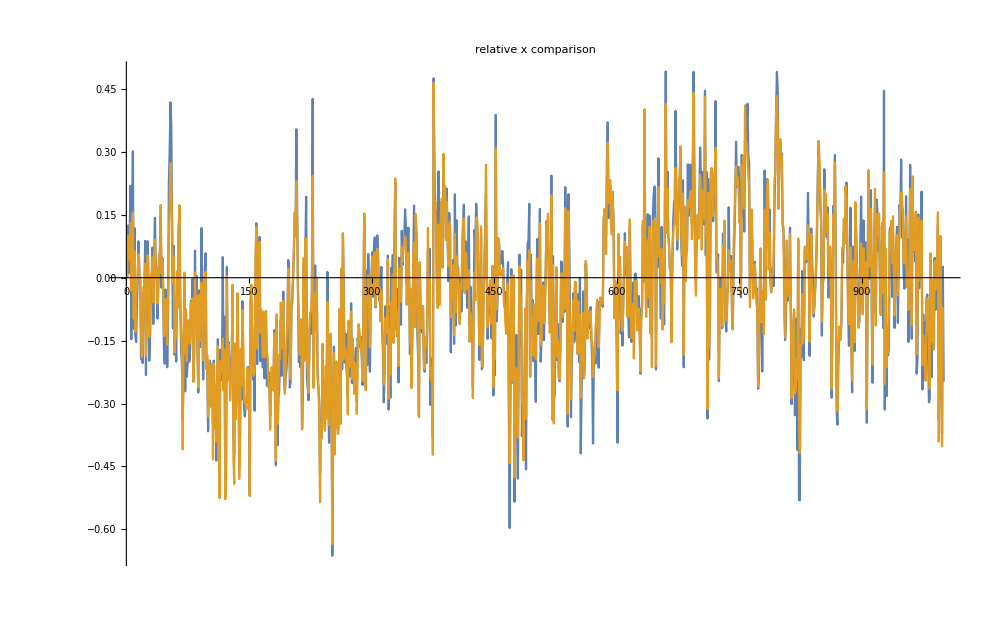

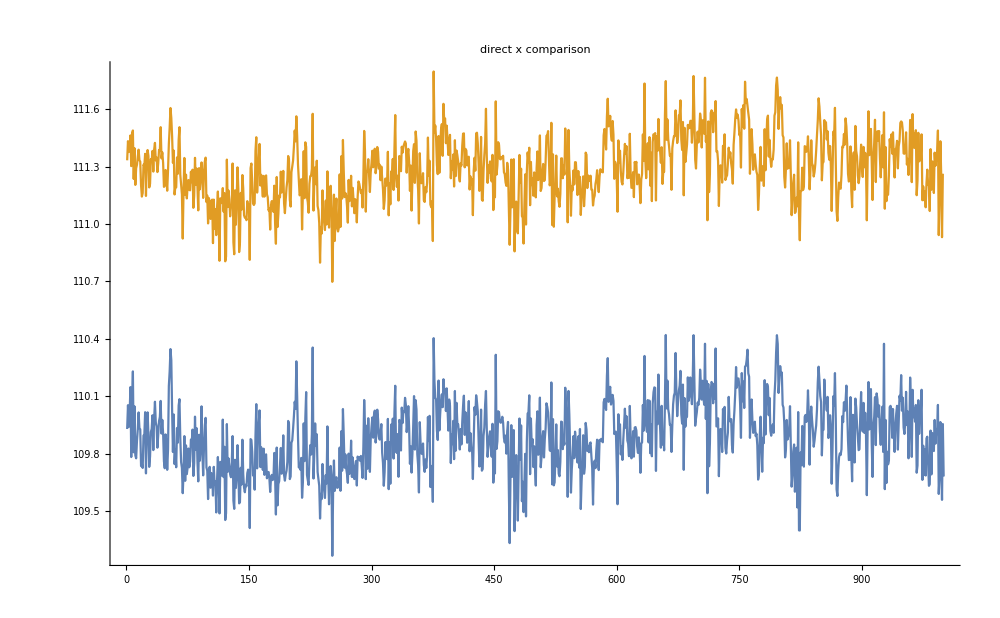

Part::partd: Part specification Fortxactual⟦1⟧ is longer than depth of object.

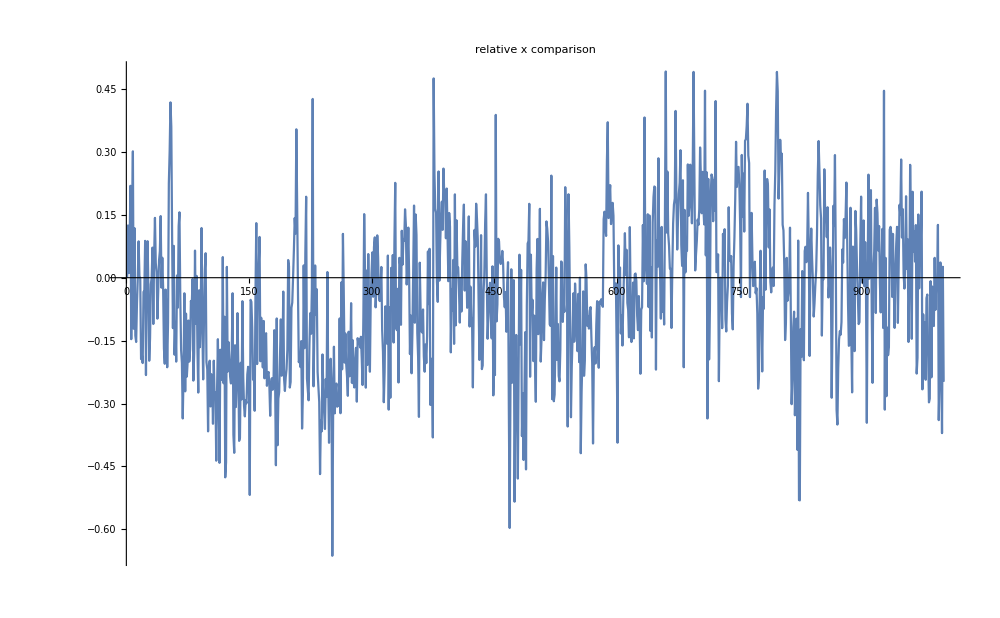

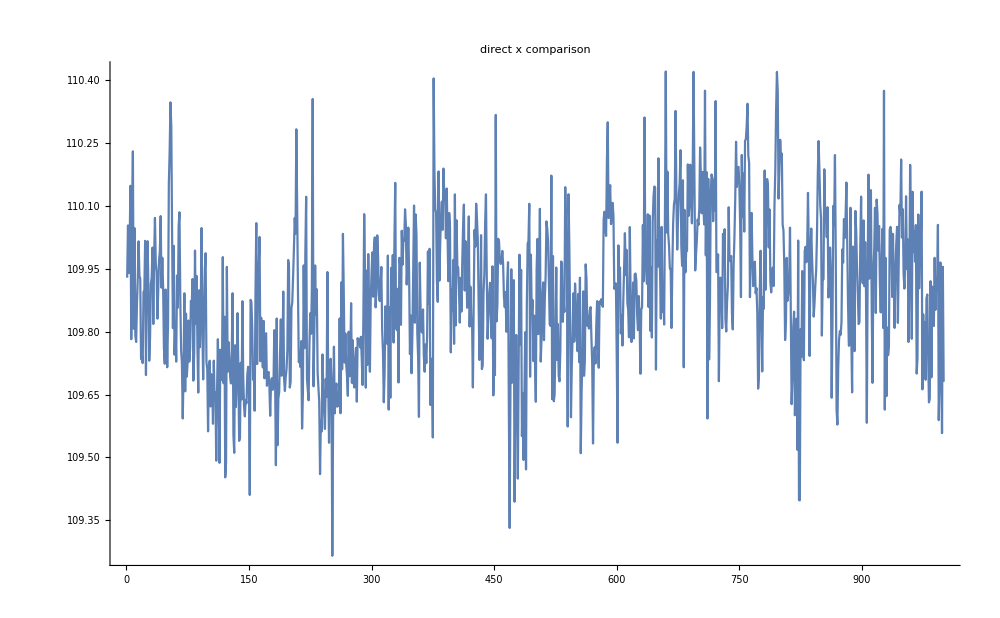

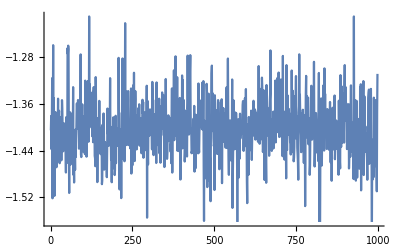

-Graphics-

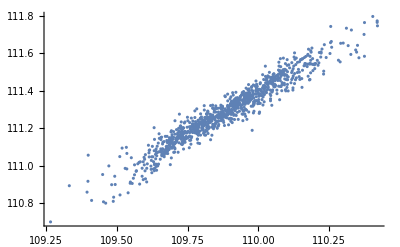

-Graphics-

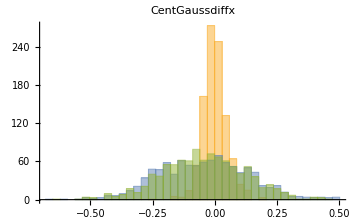

{stats for CentGaussdiffx,Mean,0.00124635,SD,0.0482017}

{stats for Fortxsave,Mean,-0.0436012,SD,0.166719}

{stats for Centroidx,Mean,-0.0425605,SD,0.181133}

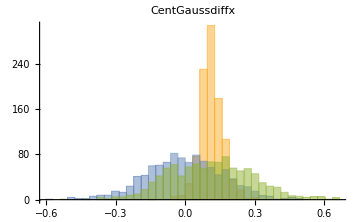

{stats for CentGaussdiffy,Mean,0.0546717,SD,0.0495191}

{stats for Fortysave,Mean,-0.103021,SD,0.158853}

{stats for Centroidy,Mean,0.157884,SD,0.175635}

```mathematica
ListLinePlot[{Centroidx-Centroidx[[1]],Fortxsave-Fortxsave[[1]]},ImageSize-> 1000,PlotLabel->"relative x comparison"]
ListLinePlot[{Centroidx,Fortxsave},ImageSize-> 1000,PlotLabel->"direct x comparison"]
ListLinePlot[{Centroidx-Centroidx[[1]],Fortxactual-Fortxactual[[1]]},ImageSize-> 1000,PlotLabel->"relative x comparison"]
ListLinePlot[{Centroidx,Fortxactual},ImageSize-> 1000,PlotLabel->"direct x comparison"]
ListLinePlot[CentGaussdiffx]
ListLinePlot[CentGaussdiffx]
(*Mean[Centroidx-Centroidx[[1]]]
Mean[Fortxactual-Fortxactual[[1]]]
Mean[CentGaussdiffx]
ListLinePlot[{Centroidx-Centroidx[[1]]},ImageSize-> 1000,PlotLabel->"relative x comparison"]
ListLinePlot[{Fortxactual-Fortxactual[[1]]},ImageSize-> 1000,PlotLabel->"relative x comparison"]*)
data1 = Transpose@{ Drop[Centroidx,-1],Fortxsave};
data2 = Transpose@{ Drop[Centroidx,-1],Fortxsave};
ListPlot[{data1}]
ListPlot[data2]
Histogram[{CentGaussdiffx-CentGaussdiffx[[1]],Centroidx-Centroidx[[1]],Fortxsave-Fortxsave[[1]]},{"Raw",40},PlotLabel->"CentGaussdiffx",ImageSize->Medium]
Print[{"stats for CentGaussdiffx","Mean", Mean[CentGaussdiffx-CentGaussdiffx[[1]]] ,"SD",StandardDeviation[CentGaussdiffx-CentGaussdiffx[[1]]]}]
Print[{"stats for Fortxsave","Mean", Mean[Fortxsave-Fortxsave[[1]]] ,"SD",StandardDeviation[Fortxsave-Fortxsave[[1]]]}]
Print[{"stats for Centroidx","Mean", Mean[Centroidx-Centroidx[[1]]] ,"SD",StandardDeviation[Centroidx-Centroidx[[1]]]}]
Histogram[{CentGaussdiffx-CentGaussdiffx[[12]],Fortxsave-Fortxsave[[12]],Centroidx-Centroidx[[12]]},{"Raw",40},PlotLabel->"CentGaussdiffx",ImageSize->Medium]
Print[{"stats for CentGaussdiffy","Mean", Mean[CentGaussdiffy-CentGaussdiffy[[1]]] ,"SD",StandardDeviation[CentGaussdiffy-CentGaussdiffy[[1]]]}]
Print[{"stats for Fortysave","Mean", Mean[Fortysave-Fortysave[[1]]] ,"SD",StandardDeviation[Fortysave-Fortysave[[1]]]}]
Print[{"stats for Centroidy","Mean", Mean[Centroidy-Centroidy[[1]]] ,"SD",StandardDeviation[Centroidy-Centroidy[[1]]]}]
(*Histogram[{CentGaussdiffxnorm},{"Raw",40},PlotLabel->"CentGaussdiffxnorm",ImageSize->Medium]
Histogram[CentGaussdiffx,{"Raw",40},PlotLabel->"CentGaussdiffx",ImageSize->Medium]
Histogram[CentGaussdiffxnorm,{"Raw",40},PlotLabel->"CentGaussdiffxnorm",ImageSize->Medium]
Histogram[Centroidx,{"Raw",40},PlotLabel->"Centroid x",ImageSize->Medium]
Histogram[Centroidx,{"Raw",40},PlotLabel->"gCentroid x",ImageSize->Medium]
Histogram[Fortxsave,{"Raw",40},PlotLabel->"gaussian x",ImageSize->Medium]
Histogram[Fortxsave,{"Raw",40},PlotLabel->"gaussian x",ImageSize->Medium]*)
```